# 私の血糖値の推移

### 経緯

1月末に、かかりつけ医にて重度の糖尿病症状が確認され直ちに入院となった。
状態は重度の糖尿病性ケトアシドーシス（極度の脱水、栄養失調、ケトーシス、高血糖）。昏睡していてもおかしくない状態だったらしい。
2週間の入院。治療は脱水状態の離脱からはじめられ、数日後より栄養状態の回復治療、ついで糖尿病治療を行なった。同時に合併症検査が行われた。
結果的に合併症はなし、退院後はインスリンによる治療と定期的な通院検査を行うものとなった。

退院後の治療は食前のインスリン投与、1日1回の高濃度インスリン投与、カロリーコントロール、血糖コントロール、を行う。

血糖は血糖測定器があり随時測定可能。食事前に血糖測定を行なっている。

本日は血糖値の測定についてと血糖値の推移について報告する。
- 周期性の確認
- ローパスによる血糖値の長期変動

### 血糖値の測定

```mathematica
jpg="/Users/kouamano/Profile/IMG_0085.jpg"
```

/Users/kouamano/Profile/IMG_0085.jpg

下の写真が血糖値の測定器（左が測定器とチップ、右が穿刺具と穿刺針）。

血糖値の測定は、まず穿刺具にて指先に穿刺し、血液を測定器のチップに塗布する。数秒で結果が出る。

測定器には過去数十件の値と測定時間が記録されており、NFCによりスマホに転送可能。転送されたスマホ側でエクセルデータを作成しさらにメール転送が可能。

```mathematica
Import[jpg]
```

-Graphics-

### Long term data

スマホから転送されてきたデータのファイル。

```mathematica
dir="/Users/kouamano/Profile/"
```

/Users/kouamano/Profile/

```mathematica
SetDirectory["/Users/kouamano/Profile"]
```

/Users/kouamano/Profile

```mathematica
files=Import["*xls"]
```

```mathematica
Length[files]
```

9

```mathematica
files[[1]][[1]]
```

{{記録時間,時間帯,血糖値,血圧,脈拍,体重,体脂肪率,食べ物とその量,薬,運動,気分,メモ},{2022-02-02 16:45:00,昼食後,379.,,,,,,,,,},{2022-02-03 06:13:00,起床,148.,,,,,,,,,},{2022-02-03 11:20:00,昼食前,396.,,,,,,,,,},{2022-02-03 16:36:00,昼食後,257.,,,,,,,,,},{2022-02-04 06:11:00,起床,177.,,,,,,,,,},{2022-02-04 11:16:00,昼食前,273.,,,,,,,,,},{2022-02-04 18:50:00,夕食前,204.,,,,,,,,,},{2022-02-05 05:57:00,深夜,98.,,,,,,,,,},{2022-02-05 12:11:00,昼食前,137.,,,,,,,,,},{2022-02-05 17:15:00,夕食前,226.,,,,,,,,,},{2022-02-06 06:08:00,起床,181.,,,,,,,,,},{2022-02-06 07:30:00,朝食後,84.,,,,,,,,,},{2022-02-06 12:20:00,昼食前,374.,,,,,,,,,},{2022-02-06 17:28:00,夕食前,241.,,,,,,,,,},{2022-02-07 06:17:00,起床,158.,,,,,,,,,},{2022-02-07 11:34:00,昼食前,293.,,,,,,,,,},{2022-02-07 16:44:00,昼食後,382.,,,,,,,,,},{2022-02-08 06:23:00,起床,152.,,,,,,,,,},{2022-02-08 12:09:00,昼食前,399.,,,,,,,,,},{2022-02-08 17:03:00,夕食前,275.,,,,,,,,,},{2022-02-09 05:51:00,深夜,116.,,,,,,,,,},{2022-02-09 11:54:00,昼食前,348.,,,,,,,,,},{2022-02-09 17:04:00,夕食前,271.,,,,,,,,,},{2022-02-10 06:12:00,起床,216.,,,,,,,,,},{2022-02-10 11:54:00,昼食前,133.,,,,,,,,,},{2022-02-10 17:01:00,夕食前,264.,,,,,,,,,},{2022-02-11 06:25:00,起床,191.,,,,,,,,,},{2022-02-11 12:00:00,昼食前,197.,,,,,,,,,},{2022-02-11 17:04:00,夕食前,224.,,,,,,,,,},{2022-02-12 06:23:00,起床,165.,,,,,,,,,},{2022-02-12 12:09:00,昼食前,210.,,,,,,,,,},{2022-02-12 17:09:00,夕食前,213.,,,,,,,,,},{2022-02-13 06:17:00,起床,217.,,,,,,,,,},{2022-02-13 12:27:00,昼食前,286.,,,,,,,,,},{2022-02-13 17:23:00,夕食前,300.,,,,,,,,,},{2022-02-14 06:12:00,起床,211.,,,,,,,,,},{2022-02-14 12:18:00,昼食前,245.,,,,,,,,,},{2022-02-14 18:49:00,夕食前,204.,,,,,,,,,},{2022-02-15 06:18:00,起床,199.,,,,,,,,,},{2022-02-15 11:59:00,昼食前,287.,,,,,,,,,},{2022-02-15 18:21:00,夕食前,205.,,,,,,,,,},{2022-02-16 06:15:00,起床,226.,,,,,,,,,},{2022-02-16 12:16:00,昼食前,308.,,,,,,,,,},{2022-02-16 18:27:00,夕食前,242.,,,,,,,,,},{2022-02-17 06:21:00,起床,238.,,,,,,,,,},{2022-02-17 12:07:00,昼食前,209.,,,,,,,,,},{2022-02-17 19:06:00,夕食後,210.,,,,,,,,,},{2022-02-18 06:11:00,起床,190.,,,,,,,,,},{2022-02-18 12:12:00,昼食前,288.,,,,,,,,,},{2022-02-18 19:21:00,夕食後,211.,,,,,,,,,},{2022-02-19 06:13:00,起床,231.,,,,,,,,,},{2022-02-19 12:17:00,昼食前,231.,,,,,,,,,},{2022-02-19 17:55:00,夕食前,179.,,,,,,,,,},{2022-02-20 06:52:00,起床,217.,,,,,,,,,},{2022-02-20 12:20:00,昼食前,243.,,,,,,,,,},{2022-02-20 17:42:00,夕食前,244.,,,,,,,,,},{2022-02-21 06:20:00,起床,197.,,,,,,,,,},{2022-02-21 12:07:00,昼食前,206.,,,,,,,,,},{2022-02-21 19:04:00,夕食後,195.,,,,,,,,,},{2022-02-22 06:36:00,起床,186.,,,,,,,,,},{2022-02-22 12:20:00,昼食前,208.,,,,,,,,,},{2022-02-22 19:44:00,夕食後,193.,,,,,,,,,},{2022-02-23 06:35:00,起床,224.,,,,,,,,,},{2022-02-23 12:00:00,昼食前,232.,,,,,,,,,},{2022-02-23 17:11:00,夕食前,194.,,,,,,,,,},{2022-02-24 06:29:00,起床,214.,,,,,,,,,},{2022-02-24 11:59:00,昼食前,233.,,,,,,,,,},{2022-02-24 19:31:00,夕食後,194.,,,,,,,,,},{2022-02-25 06:19:00,起床,224.,,,,,,,,,},{2022-02-25 12:26:00,昼食前,206.,,,,,,,,,},{2022-02-25 19:37:00,夕食後,188.,,,,,,,,,},{2022-02-26 06:24:00,起床,223.,,,,,,,,,},{2022-02-26 11:56:00,昼食前,261.,,,,,,,,,},{2022-02-26 18:00:00,夕食前,180.,,,,,,,,,},{2022-02-27 06:27:00,起床,208.,,,,,,,,,},{2022-02-27 12:14:00,昼食前,212.,,,,,,,,,},{2022-02-27 17:25:00,夕食前,161.,,,,,,,,,},{2022-02-28 06:31:00,起床,197.,,,,,,,,,},{2022-02-28 11:58:00,昼食前,221.,,,,,,,,,},{2022-02-28 18:32:00,夕食前,184.,,,,,,,,,},{2022-03-01 06:13:00,起床,195.,,,,,,,,,},{2022-03-01 12:08:00,昼食前,213.,,,,,,,,,},{2022-03-01 18:30:00,夕食前,173.,,,,,,,,,},{2022-03-02 06:29:00,起床,192.,,,,,,,,,},{2022-03-02 12:07:00,昼食前,239.,,,,,,,,,},{2022-03-02 18:40:00,夕食前,187.,,,,,,,,,},{2022-03-03 06:23:00,起床,177.,,,,,,,,,},{2022-03-03 12:32:00,昼食前,209.,,,,,,,,,},{2022-03-03 18:53:00,夕食前,209.,,,,,,,,,},{2022-03-04 12:15:00,昼食前,175.,,,,,,,,,},{2022-03-04 18:59:00,夕食前,173.,,,,,,,,,},{2022-03-05 06:18:00,起床,194.,,,,,,,,,},{2022-03-05 11:58:00,昼食前,163.,,,,,,,,,},{2022-03-05 18:01:00,夕食前,214.,,,,,,,,,},{2022-03-06 06:15:00,起床,145.,,,,,,,,,},{2022-03-06 12:24:00,昼食前,182.,,,,,,,,,},{2022-03-06 18:14:00,夕食前,195.,,,,,,,,,},{2022-03-07 06:16:00,起床,175.,,,,,,,,,},{2022-03-07 12:00:00,昼食前,214.,,,,,,,,,},{2022-03-07 18:52:00,夕食前,168.,,,,,,,,,},{2022-03-08 06:29:00,起床,162.,,,,,,,,,},{2022-03-08 12:48:00,昼食前,165.,,,,,,,,,},{2022-03-08 18:31:00,夕食前,172.,,,,,,,,,},{2022-03-09 06:09:00,起床,157.,,,,,,,,,},{2022-03-09 11:50:00,昼食前,202.,,,,,,,,,},{2022-03-09 18:26:00,夕食前,152.,,,,,,,,,},{2022-03-10 06:20:00,起床,168.,,,,,,,,,},{2022-03-10 12:07:00,昼食前,182.,,,,,,,,,},{2022-03-10 19:08:00,夕食後,144.,,,,,,,,,},{2022-03-11 06:06:00,起床,150.,,,,,,,,,},{2022-03-11 11:58:00,昼食前,161.,,,,,,,,,},{2022-03-11 18:11:00,夕食前,173.,,,,,,,,,},{2022-03-12 06:09:00,起床,132.,,,,,,,,,},{2022-03-12 12:42:00,昼食前,207.,,,,,,,,,},{2022-03-12 18:06:00,夕食前,262.,,,,,,,,,},{2022-03-13 06:24:00,起床,184.,,,,,,,,,},{2022-03-13 12:12:00,昼食前,170.,,,,,,,,,},{2022-03-13 18:07:00,夕食前,168.,,,,,,,,,},{2022-03-14 06:14:00,起床,154.,,,,,,,,,},{2022-03-14 11:59:00,昼食前,197.,,,,,,,,,},{2022-03-14 18:45:00,夕食前,134.,,,,,,,,,},{2022-03-15 06:13:00,起床,129.,,,,,,,,,},{2022-03-15 12:04:00,昼食前,133.,,,,,,,,,},{2022-03-15 18:25:00,夕食前,160.,,,,,,,,,},{2022-03-16 06:18:00,起床,142.,,,,,,,,,},{2022-03-16 12:02:00,昼食前,192.,,,,,,,,,},{2022-03-16 17:56:00,夕食前,145.,,,,,,,,,},{2022-03-17 06:18:00,起床,104.,,,,,,,,,},{2022-03-17 12:33:00,昼食前,173.,,,,,,,,,},{2022-03-17 18:28:00,夕食前,149.,,,,,,,,,},{2022-03-18 06:16:00,起床,124.,,,,,,,,,},{2022-03-18 12:42:00,昼食前,202.,,,,,,,,,},{2022-03-18 19:30:00,夕食後,144.,,,,,,,,,},{2022-03-19 06:27:00,起床,178.,,,,,,,,,},{2022-03-19 12:11:00,昼食前,164.,,,,,,,,,},{2022-03-19 18:11:00,夕食前,161.,,,,,,,,,},{2022-03-20 07:13:00,朝食前,159.,,,,,,,,,},{2022-03-20 12:11:00,昼食前,132.,,,,,,,,,},{2022-03-20 18:27:00,夕食前,147.,,,,,,,,,},{2022-03-21 06:34:00,起床,169.,,,,,,,,,},{2022-03-21 13:00:00,昼食前,192.,,,,,,,,,},{2022-03-21 18:22:00,夕食前,175.,,,,,,,,,},{2022-03-23 11:17:00,昼食前,183.,,,,,,,,,},{2022-03-23 16:49:00,昼食後,148.,,,,,,,,,},{2022-03-24 06:45:00,起床,183.,,,,,,,,,},{2022-03-24 11:56:00,昼食前,131.,,,,,,,,,},{2022-03-24 18:37:00,夕食前,130.,,,,,,,,,},{2022-03-25 06:12:00,起床,134.,,,,,,,,,},{2022-03-25 12:05:00,昼食前,134.,,,,,,,,,},{2022-03-25 21:36:00,就寝,114.,,,,,,,,,},{2022-03-26 09:09:00,朝食後,123.,,,,,,,,,},{2022-03-26 12:08:00,昼食前,108.,,,,,,,,,},{2022-03-26 18:43:00,夕食前,221.,,,,,,,,,},{2022-03-27 07:51:00,朝食前,185.,,,,,,,,,},{2022-03-27 12:41:00,昼食前,141.,,,,,,,,,},{2022-03-27 18:29:00,夕食前,180.,,,,,,,,,},{2022-03-28 07:40:00,朝食前,129.,,,,,,,,,},{2022-03-28 12:00:00,昼食前,132.,,,,,,,,,},{2022-03-28 18:49:00,夕食前,123.,,,,,,,,,},{2022-03-29 06:28:00,起床,124.,,,,,,,,,},{2022-03-29 12:06:00,昼食前,159.,,,,,,,,,},{2022-03-29 19:50:00,夕食後,122.,,,,,,,,,},{2022-03-31 07:15:00,朝食前,141.,,,,,,,,,},{2022-03-31 12:04:00,昼食前,128.,,,,,,,,,},{2022-03-31 18:02:00,夕食前,274.,,,,,,,,,},{2022-04-02 06:47:00,起床,90.,,,,,,,,,},{2022-04-02 12:42:00,昼食前,143.,,,,,,,,,},{2022-04-02 18:11:00,夕食前,105.,,,,,,,,,},{2022-04-03 06:46:00,起床,130.,,,,,,,,,},{2022-04-03 12:58:00,昼食前,95.,,,,,,,,,},{2022-04-03 18:33:00,夕食前,231.,,,,,,,,,},{2022-04-04 06:40:00,起床,115.,,,,,,,,,},{2022-04-04 12:15:00,昼食前,174.,,,,,,,,,},{2022-04-04 19:50:00,夕食後,115.,,,,,,,,,},{2022-04-05 06:30:00,起床,125.,,,,,,,,,},{2022-04-05 12:00:00,昼食前,133.,,,,,,,,,},{2022-04-05 20:25:00,夕食後,125.,,,,,,,,,},{2022-04-06 07:23:00,朝食前,137.,,,,,,,,,},{2022-04-06 12:04:00,昼食前,106.,,,,,,,,,},{2022-04-06 18:15:00,夕食前,132.,,,,,,,,,},{2022-04-07 06:36:00,起床,152.,,,,,,,,,},{2022-04-07 12:00:00,昼食前,144.,,,,,,,,,},{2022-04-07 18:17:00,夕食前,121.,,,,,,,,,},{2022-04-08 06:15:00,起床,128.,,,,,,,,,},{2022-04-08 12:07:00,昼食前,157.,,,,,,,,,},{2022-04-08 19:27:00,夕食後,112.,,,,,,,,,},{2022-04-09 07:32:00,朝食前,153.,,,,,,,,,},{2022-04-09 13:07:00,昼食後,244.,,,,,,,,,},{2022-04-09 17:52:00,夕食前,130.,,,,,,,,,},{2022-04-10 06:26:00,起床,127.,,,,,,,,,},{2022-04-10 12:33:00,昼食前,243.,,,,,,,,,},{2022-04-10 17:03:00,夕食前,92.,,,,,,,,,},{2022-04-11 06:42:00,起床,113.,,,,,,,,,},{2022-04-11 11:57:00,昼食前,168.,,,,,,,,,},{2022-04-11 18:05:00,夕食前,148.,,,,,,,,,},{2022-04-12 06:41:00,起床,150.,,,,,,,,,},{2022-04-12 11:47:00,昼食前,158.,,,,,,,,,},{2022-04-12 18:16:00,夕食前,128.,,,,,,,,,},{2022-04-13 07:06:00,朝食前,118.,,,,,,,,,},{2022-04-13 12:06:00,昼食前,163.,,,,,,,,,},{2022-04-13 19:13:00,夕食後,128.,,,,,,,,,},{2022-04-14 06:38:00,起床,122.,,,,,,,,,},{2022-04-14 12:07:00,昼食前,123.,,,,,,,,,},{2022-04-14 18:45:00,夕食前,161.,,,,,,,,,},{2022-04-15 06:43:00,起床,131.,,,,,,,,,},{2022-04-15 12:06:00,昼食前,86.,,,,,,,,,},{2022-04-15 18:47:00,夕食前,106.,,,,,,,,,},{2022-04-16 06:31:00,起床,126.,,,,,,,,,},{2022-04-16 13:10:00,昼食後,100.,,,,,,,,,},{2022-04-16 18:16:00,夕食前,116.,,,,,,,,,},{2022-04-17 08:53:00,朝食前,142.,,,,,,,,,},{2022-04-17 12:53:00,昼食前,108.,,,,,,,,,},{2022-04-17 18:20:00,夕食前,139.,,,,,,,,,},{2022-04-18 06:31:00,起床,151.,,,,,,,,,},{2022-04-18 12:24:00,昼食前,127.,,,,,,,,,},{2022-04-18 18:43:00,夕食前,95.,,,,,,,,,},{2022-04-20 06:40:00,起床,129.,,,,,,,,,},{2022-04-20 12:07:00,昼食前,105.,,,,,,,,,},{2022-04-20 18:29:00,夕食前,89.,,,,,,,,,},{2022-04-21 06:39:00,起床,115.,,,,,,,,,},{2022-04-21 11:51:00,昼食前,142.,,,,,,,,,},{2022-04-21 18:06:00,夕食前,138.,,,,,,,,,},{2022-04-22 06:41:00,起床,143.,,,,,,,,,},{2022-04-22 12:00:00,昼食前,114.,,,,,,,,,},{2022-04-22 19:00:00,夕食前,113.,,,,,,,,,},{2022-04-23 06:29:00,起床,138.,,,,,,,,,},{2022-04-23 11:53:00,昼食前,129.,,,,,,,,,},{2022-04-23 17:23:00,夕食前,175.,,,,,,,,,},{2022-04-24 08:11:00,朝食前,147.,,,,,,,,,},{2022-04-24 12:24:00,昼食前,114.,,,,,,,,,},{2022-04-24 17:59:00,夕食前,188.,,,,,,,,,},{2022-04-25 06:49:00,起床,145.,,,,,,,,,},{2022-04-25 12:09:00,昼食前,166.,,,,,,,,,},{2022-04-25 18:57:00,夕食前,113.,,,,,,,,,},{2022-04-26 06:13:00,起床,142.,,,,,,,,,},{2022-04-26 11:56:00,昼食前,127.,,,,,,,,,},{2022-04-26 18:25:00,夕食前,107.,,,,,,,,,},{2022-04-27 06:53:00,起床,113.,,,,,,,,,},{2022-04-27 08:36:00,朝食前,64.,,,,,,,,,},{2022-04-27 11:56:00,昼食前,119.,,,,,,,,,},{2022-04-27 18:42:00,夕食前,110.,,,,,,,,,}}

```mathematica
Drop[files[[4]][[1]],26]
```

{{2022-04-28 06:43:00,起床,119.,,,,,,,,,},{2022-04-28 12:05:00,昼食前,130.,,,,,,,,,},{2022-04-28 19:01:00,夕食後,122.,,,,,,,,,},{2022-04-29 06:26:00,起床,92.,,,,,,,,,},{2022-04-29 12:03:00,昼食前,112.,,,,,,,,,},{2022-04-29 17:33:00,夕食前,109.,,,,,,,,,},{2022-04-30 06:11:00,起床,114.,,,,,,,,,},{2022-04-30 12:23:00,昼食前,99.,,,,,,,,,},{2022-04-30 19:00:00,夕食前,127.,,,,,,,,,},{2022-05-01 06:34:00,起床,108.,,,,,,,,,},{2022-05-01 13:04:00,昼食後,130.,,,,,,,,,},{2022-05-01 18:23:00,夕食前,157.,,,,,,,,,},{2022-05-02 06:41:00,起床,115.,,,,,,,,,},{2022-05-02 12:07:00,昼食前,160.,,,,,,,,,},{2022-05-02 17:54:00,夕食前,132.,,,,,,,,,},{2022-05-03 06:35:00,起床,130.,,,,,,,,,},{2022-05-03 12:03:00,昼食前,129.,,,,,,,,,},{2022-05-03 18:44:00,夕食前,163.,,,,,,,,,},{2022-05-04 06:37:00,起床,151.,,,,,,,,,},{2022-05-04 12:25:00,昼食前,139.,,,,,,,,,},{2022-05-04 19:23:00,夕食後,163.,,,,,,,,,},{2022-05-05 16:21:00,昼食後,85.,,,,,,,,,},{2022-05-06 18:35:00,夕食前,147.,,,,,,,,,},{2022-05-07 07:33:00,朝食前,140.,,,,,,,,,},{2022-05-07 11:56:00,昼食前,102.,,,,,,,,,},{2022-05-07 18:08:00,夕食前,137.,,,,,,,,,},{2022-05-08 06:58:00,起床,145.,,,,,,,,,},{2022-05-08 11:39:00,昼食前,115.,,,,,,,,,},{2022-05-08 17:40:00,夕食前,90.,,,,,,,,,},{2022-05-09 06:41:00,起床,171.,,,,,,,,,},{2022-05-09 11:49:00,昼食前,136.,,,,,,,,,},{2022-05-09 18:34:00,夕食前,122.,,,,,,,,,},{2022-05-10 06:50:00,起床,132.,,,,,,,,,},{2022-05-10 12:11:00,昼食後,131.,,,,,,,,,},{2022-05-10 19:02:00,夕食後,114.,,,,,,,,,},{2022-05-11 06:42:00,起床,138.,,,,,,,,,},{2022-05-11 12:16:00,昼食前,142.,,,,,,,,,},{2022-05-11 18:02:00,夕食前,147.,,,,,,,,,},{2022-05-12 06:54:00,起床,160.,,,,,,,,,},{2022-05-12 11:51:00,昼食前,99.,,,,,,,,,},{2022-05-12 18:00:00,夕食前,112.,,,,,,,,,},{2022-05-13 06:12:00,起床,121.,,,,,,,,,},{2022-05-13 12:02:00,昼食前,121.,,,,,,,,,},{2022-05-13 18:54:00,夕食前,124.,,,,,,,,,},{2022-05-14 06:54:00,起床,136.,,,,,,,,,},{2022-05-14 13:09:00,昼食後,146.,,,,,,,,,},{2022-05-14 18:34:00,夕食前,183.,,,,,,,,,},{2022-05-15 06:46:00,起床,139.,,,,,,,,,},{2022-05-15 11:42:00,昼食前,97.,,,,,,,,,},{2022-05-15 17:59:00,夕食前,113.,,,,,,,,,},{2022-05-16 06:16:00,起床,122.,,,,,,,,,},{2022-05-16 12:02:00,昼食前,92.,,,,,,,,,},{2022-05-16 19:27:00,夕食後,107.,,,,,,,,,},{2022-05-17 06:54:00,起床,107.,,,,,,,,,},{2022-05-17 11:45:00,昼食前,79.,,,,,,,,,},{2022-05-17 19:04:00,夕食後,123.,,,,,,,,,},{2022-05-18 06:18:00,起床,152.,,,,,,,,,},{2022-05-18 11:48:00,昼食前,150.,,,,,,,,,},{2022-05-18 19:35:00,夕食後,111.,,,,,,,,,},{2022-05-19 06:59:00,起床,146.,,,,,,,,,},{2022-05-19 11:42:00,昼食前,103.,,,,,,,,,},{2022-05-19 19:39:00,夕食後,95.,,,,,,,,,},{2022-05-20 06:38:00,起床,91.,,,,,,,,,},{2022-05-20 11:57:00,昼食前,130.,,,,,,,,,},{2022-05-20 18:14:00,夕食前,143.,,,,,,,,,},{2022-05-21 07:28:00,朝食前,131.,,,,,,,,,},{2022-05-21 12:30:00,昼食前,200.,,,,,,,,,},{2022-05-21 18:01:00,夕食前,138.,,,,,,,,,},{2022-05-22 07:21:00,朝食前,166.,,,,,,,,,},{2022-05-22 12:10:00,昼食前,160.,,,,,,,,,},{2022-05-22 18:09:00,夕食前,132.,,,,,,,,,},{2022-05-23 06:28:00,起床,131.,,,,,,,,,},{2022-05-23 11:53:00,昼食前,97.,,,,,,,,,},{2022-05-23 19:08:00,夕食後,121.,,,,,,,,,},{2022-05-24 06:35:00,起床,131.,,,,,,,,,},{2022-05-24 11:58:00,昼食前,138.,,,,,,,,,},{2022-05-24 19:32:00,夕食後,106.,,,,,,,,,},{2022-05-25 06:17:00,起床,88.,,,,,,,,,},{2022-05-25 12:05:00,昼食前,82.,,,,,,,,,},{2022-05-25 18:36:00,夕食前,120.,,,,,,,,,},{2022-05-26 06:19:00,起床,126.,,,,,,,,,},{2022-05-26 12:00:00,昼食前,119.,,,,,,,,,},{2022-05-26 19:08:00,夕食後,120.,,,,,,,,,},{2022-05-27 06:21:00,起床,123.,,,,,,,,,},{2022-05-27 13:38:00,昼食後,119.,,,,,,,,,},{2022-05-27 17:55:00,夕食前,91.,,,,,,,,,},{2022-05-28 06:47:00,起床,156.,,,,,,,,,},{2022-05-28 12:14:00,昼食前,124.,,,,,,,,,},{2022-05-28 18:58:00,夕食前,106.,,,,,,,,,},{2022-05-29 06:05:00,起床,118.,,,,,,,,,},{2022-05-29 11:54:00,昼食前,124.,,,,,,,,,},{2022-05-29 18:33:00,夕食前,133.,,,,,,,,,},{2022-05-30 06:39:00,起床,133.,,,,,,,,,},{2022-05-30 11:57:00,昼食前,118.,,,,,,,,,},{2022-05-30 18:11:00,夕食前,114.,,,,,,,,,},{2022-05-31 06:39:00,起床,122.,,,,,,,,,},{2022-05-31 12:08:00,昼食前,127.,,,,,,,,,},{2022-05-31 18:04:00,夕食前,112.,,,,,,,,,},{2022-06-01 06:16:00,起床,126.,,,,,,,,,},{2022-06-01 11:45:00,昼食前,115.,,,,,,,,,},{2022-06-01 19:33:00,夕食後,88.,,,,,,,,,},{2022-06-02 06:36:00,起床,126.,,,,,,,,,},{2022-06-02 12:14:00,昼食前,131.,,,,,,,,,},{2022-06-02 18:38:00,夕食前,88.,,,,,,,,,},{2022-06-03 17:43:00,夕食前,133.,,,,,,,,,},{2022-06-04 07:34:00,朝食前,126.,,,,,,,,,},{2022-06-04 12:13:00,昼食前,137.,,,,,,,,,},{2022-06-04 17:53:00,夕食前,121.,,,,,,,,,},{2022-06-05 07:23:00,朝食前,129.,,,,,,,,,},{2022-06-05 12:26:00,昼食前,129.,,,,,,,,,},{2022-06-05 17:55:00,夕食前,146.,,,,,,,,,},{2022-06-06 07:00:00,起床,138.,,,,,,,,,},{2022-06-06 12:04:00,昼食前,120.,,,,,,,,,},{2022-06-06 18:35:00,夕食前,124.,,,,,,,,,},{2022-06-07 06:54:00,起床,136.,,,,,,,,,},{2022-06-07 12:03:00,昼食前,140.,,,,,,,,,},{2022-06-07 18:45:00,夕食前,114.,,,,,,,,,},{2022-06-08 07:14:00,朝食前,118.,,,,,,,,,},{2022-06-08 11:50:00,昼食前,119.,,,,,,,,,},{2022-06-08 19:03:00,夕食後,120.,,,,,,,,,},{2022-06-09 06:41:00,起床,161.,,,,,,,,,},{2022-06-09 11:53:00,昼食前,113.,,,,,,,,,},{2022-06-09 18:49:00,夕食前,126.,,,,,,,,,},{2022-06-10 06:11:00,起床,125.,,,,,,,,,},{2022-06-10 11:48:00,昼食前,142.,,,,,,,,,},{2022-06-10 18:36:00,夕食前,115.,,,,,,,,,},{2022-06-11 06:49:00,起床,137.,,,,,,,,,},{2022-06-11 12:11:00,昼食前,150.,,,,,,,,,},{2022-06-11 17:57:00,夕食前,113.,,,,,,,,,},{2022-06-12 08:12:00,朝食前,120.,,,,,,,,,},{2022-06-12 12:38:00,昼食前,117.,,,,,,,,,},{2022-06-12 18:25:00,夕食前,126.,,,,,,,,,},{2022-06-13 06:48:00,起床,156.,,,,,,,,,},{2022-06-13 12:01:00,昼食前,124.,,,,,,,,,},{2022-06-13 19:44:00,夕食後,124.,,,,,,,,,},{2022-06-14 06:45:00,起床,122.,,,,,,,,,},{2022-06-14 12:22:00,昼食前,136.,,,,,,,,,},{2022-06-14 19:19:00,夕食後,127.,,,,,,,,,},{2022-06-16 06:47:00,起床,141.,,,,,,,,,},{2022-06-16 12:21:00,昼食前,116.,,,,,,,,,},{2022-06-16 19:03:00,夕食後,132.,,,,,,,,,},{2022-06-17 06:25:00,起床,142.,,,,,,,,,},{2022-06-17 12:06:00,昼食前,128.,,,,,,,,,},{2022-06-17 18:45:00,夕食前,112.,,,,,,,,,},{2022-06-18 07:07:00,朝食前,124.,,,,,,,,,},{2022-06-18 12:05:00,昼食前,111.,,,,,,,,,},{2022-06-18 18:41:00,夕食前,183.,,,,,,,,,},{2022-06-19 07:31:00,朝食前,147.,,,,,,,,,},{2022-06-19 12:17:00,昼食前,118.,,,,,,,,,},{2022-06-19 18:17:00,夕食前,79.,,,,,,,,,},{2022-06-20 07:05:00,朝食前,114.,,,,,,,,,},{2022-06-20 12:02:00,昼食前,107.,,,,,,,,,},{2022-06-20 19:28:00,夕食後,116.,,,,,,,,,},{2022-06-21 07:13:00,朝食前,128.,,,,,,,,,},{2022-06-21 12:02:00,昼食前,118.,,,,,,,,,},{2022-06-21 18:59:00,夕食前,136.,,,,,,,,,},{2022-06-22 06:31:00,起床,131.,,,,,,,,,},{2022-06-22 11:51:00,昼食前,126.,,,,,,,,,},{2022-06-22 19:01:00,夕食後,107.,,,,,,,,,},{2022-06-23 07:15:00,朝食前,133.,,,,,,,,,},{2022-06-23 12:37:00,昼食前,168.,,,,,,,,,},{2022-06-23 18:21:00,夕食前,117.,,,,,,,,,},{2022-06-24 06:36:00,起床,110.,,,,,,,,,},{2022-06-24 12:01:00,昼食前,148.,,,,,,,,,},{2022-06-24 20:27:00,夕食後,121.,,,,,,,,,},{2022-06-25 07:33:00,朝食前,138.,,,,,,,,,},{2022-06-25 12:04:00,昼食前,156.,,,,,,,,,},{2022-06-25 19:15:00,夕食後,148.,,,,,,,,,},{2022-06-26 11:25:00,昼食前,132.,,,,,,,,,},{2022-06-26 18:25:00,夕食前,228.,,,,,,,,,},{2022-06-27 07:08:00,朝食前,119.,,,,,,,,,},{2022-06-27 12:09:00,昼食前,160.,,,,,,,,,},{2022-06-27 18:25:00,夕食前,99.,,,,,,,,,},{2022-06-28 07:02:00,朝食前,106.,,,,,,,,,},{2022-06-28 12:13:00,昼食前,131.,,,,,,,,,},{2022-06-30 06:44:00,起床,146.,,,,,,,,,},{2022-06-30 12:12:00,昼食前,147.,,,,,,,,,},{2022-06-30 19:14:00,夕食後,131.,,,,,,,,,},{2022-07-01 19:13:00,夕食後,119.,,,,,,,,,},{2022-07-02 07:22:00,朝食前,110.,,,,,,,,,},{2022-07-02 12:13:00,昼食前,146.,,,,,,,,,},{2022-07-02 18:43:00,夕食前,203.,,,,,,,,,},{2022-07-03 08:08:00,朝食前,104.,,,,,,,,,},{2022-07-03 14:30:00,昼食後,208.,,,,,,,,,},{2022-07-03 18:26:00,夕食前,78.,,,,,,,,,},{2022-07-04 06:42:00,起床,121.,,,,,,,,,},{2022-07-04 11:59:00,昼食前,103.,,,,,,,,,},{2022-07-04 19:27:00,夕食後,117.,,,,,,,,,},{2022-07-05 07:35:00,朝食前,126.,,,,,,,,,},{2022-07-05 11:53:00,昼食前,141.,,,,,,,,,},{2022-07-05 19:04:00,夕食後,99.,,,,,,,,,},{2022-07-06 07:19:00,朝食前,82.,,,,,,,,,},{2022-07-06 12:01:00,昼食前,89.,,,,,,,,,},{2022-07-06 19:11:00,夕食後,96.,,,,,,,,,},{2022-07-07 06:42:00,起床,124.,,,,,,,,,},{2022-07-07 11:58:00,昼食前,144.,,,,,,,,,},{2022-07-07 18:16:00,夕食前,107.,,,,,,,,,},{2022-07-08 07:16:00,朝食前,106.,,,,,,,,,},{2022-07-08 11:55:00,昼食前,114.,,,,,,,,,},{2022-07-08 19:12:00,夕食後,136.,,,,,,,,,},{2022-07-09 07:22:00,朝食前,128.,,,,,,,,,},{2022-07-09 13:55:00,昼食後,147.,,,,,,,,,},{2022-07-09 18:56:00,夕食前,121.,,,,,,,,,},{2022-07-10 08:21:00,朝食前,129.,,,,,,,,,},{2022-07-10 18:34:00,夕食前,232.,,,,,,,,,},{2022-07-11 06:58:00,起床,108.,,,,,,,,,},{2022-07-11 11:51:00,昼食前,109.,,,,,,,,,},{2022-07-11 19:33:00,夕食後,157.,,,,,,,,,},{2022-07-12 07:15:00,朝食前,143.,,,,,,,,,},{2022-07-12 11:49:00,昼食前,104.,,,,,,,,,},{2022-07-12 18:11:00,夕食後,107.,,,,,,,,,},{2022-07-14 06:48:00,起床,146.,,,,,,,,,},{2022-07-14 12:12:00,昼食前,107.,,,,,,,,,},{2022-07-14 19:14:00,夕食後,135.,,,,,,,,,},{2022-07-15 07:16:00,朝食前,140.,,,,,,,,,},{2022-07-15 12:19:00,昼食前,117.,,,,,,,,,},{2022-07-15 19:25:00,夕食後,129.,,,,,,,,,},{2022-07-16 08:19:00,朝食前,143.,,,,,,,,,},{2022-07-16 12:52:00,昼食前,114.,,,,,,,,,},{2022-07-17 08:03:00,朝食前,143.,,,,,,,,,},{2022-07-17 18:09:00,夕食前,167.,,,,,,,,,}}

```mathematica
Drop[files[[9]][[1]],90]
```

{{2022-07-18 09:44:00,朝食後,144.,,,,,,,,,},{2022-07-18 17:46:00,夕食前,182.,,,,,,,,,},{2022-07-19 07:40:00,朝食前,109.,,,,,,,,,},{2022-07-19 12:05:00,昼食前,126.,,,,,,,,,},{2022-07-19 19:01:00,夕食後,125.,,,,,,,,,},{2022-07-20 07:17:00,朝食前,115.,,,,,,,,,},{2022-07-20 11:58:00,昼食前,105.,,,,,,,,,},{2022-07-20 18:44:00,夕食前,125.,,,,,,,,,},{2022-07-21 12:47:00,昼食前,180.,,,,,,,,,},{2022-07-21 19:04:00,夕食後,117.,,,,,,,,,},{2022-07-22 07:17:00,朝食前,125.,,,,,,,,,},{2022-07-22 12:03:00,昼食前,113.,,,,,,,,,},{2022-07-22 19:57:00,夕食後,99.,,,,,,,,,},{2022-07-24 09:31:00,朝食後,87.,,,,,,,,,},{2022-07-24 13:47:00,昼食後,84.,,,,,,,,,},{2022-07-24 18:03:00,夕食前,106.,,,,,,,,,},{2022-07-25 08:12:00,朝食前,122.,,,,,,,,,},{2022-07-25 11:58:00,昼食前,133.,,,,,,,,,},{2022-07-25 19:00:00,夕食前,121.,,,,,,,,,},{2022-07-26 07:32:00,朝食前,109.,,,,,,,,,},{2022-07-26 20:18:00,夕食後,121.,,,,,,,,,},{2022-07-28 06:42:00,起床,104.,,,,,,,,,},{2022-07-28 12:09:00,昼食前,112.,,,,,,,,,},{2022-07-28 18:17:00,夕食前,112.,,,,,,,,,},{2022-07-29 07:28:00,朝食前,136.,,,,,,,,,},{2022-07-29 12:09:00,昼食前,116.,,,,,,,,,},{2022-07-29 19:35:00,夕食後,132.,,,,,,,,,},{2022-07-30 11:20:00,昼食前,137.,,,,,,,,,},{2022-07-30 18:18:00,夕食前,136.,,,,,,,,,},{2022-07-31 11:30:00,昼食前,145.,,,,,,,,,},{2022-07-31 18:19:00,夕食前,238.,,,,,,,,,},{2022-08-01 08:42:00,朝食前,133.,,,,,,,,,},{2022-08-01 13:44:00,昼食後,112.,,,,,,,,,},{2022-08-01 19:19:00,夕食後,100.,,,,,,,,,},{2022-08-02 07:53:00,朝食前,118.,,,,,,,,,},{2022-08-02 12:11:00,昼食前,147.,,,,,,,,,},{2022-08-02 18:39:00,夕食前,98.,,,,,,,,,},{2022-08-03 07:22:00,朝食前,90.,,,,,,,,,},{2022-08-03 11:55:00,昼食前,102.,,,,,,,,,},{2022-08-03 18:43:00,夕食前,97.,,,,,,,,,},{2022-08-04 07:25:00,朝食前,88.,,,,,,,,,},{2022-08-04 12:07:00,昼食前,137.,,,,,,,,,},{2022-08-04 19:50:00,夕食後,115.,,,,,,,,,},{2022-08-06 07:31:00,朝食前,109.,,,,,,,,,},{2022-08-06 18:24:00,夕食前,112.,,,,,,,,,},{2022-08-07 11:49:00,昼食前,144.,,,,,,,,,},{2022-08-08 09:48:00,朝食後,136.,,,,,,,,,},{2022-08-09 08:42:00,朝食前,137.,,,,,,,,,},{2022-08-10 07:54:00,朝食前,92.,,,,,,,,,},{2022-08-11 09:26:00,朝食後,124.,,,,,,,,,},{2022-08-12 10:02:00,朝食後,139.,,,,,,,,,},{2022-08-13 10:35:00,朝食後,170.,,,,,,,,,},{2022-08-14 12:33:00,昼食前,146.,,,,,,,,,},{2022-08-15 17:43:00,夕食前,143.,,,,,,,,,},{2022-08-16 08:51:00,朝食前,97.,,,,,,,,,},{2022-08-17 06:51:00,起床,109.,,,,,,,,,},{2022-08-18 19:13:00,夕食後,104.,,,,,,,,,},{2022-08-19 09:44:00,朝食後,151.,,,,,,,,,},{2022-08-20 11:28:00,昼食前,140.,,,,,,,,,},{2022-08-21 07:22:00,朝食前,138.,,,,,,,,,},{2022-08-22 11:44:00,昼食前,164.,,,,,,,,,},{2022-08-25 19:07:00,夕食後,124.,,,,,,,,,},{2022-08-26 06:44:00,起床,141.,,,,,,,,,},{2022-08-27 07:41:00,朝食前,147.,,,,,,,,,},{2022-08-29 11:54:00,昼食前,79.,,,,,,,,,},{2022-08-31 08:22:00,朝食前,137.,,,,,,,,,},{2022-09-03 18:08:00,夕食前,130.,,,,,,,,,},{2022-09-05 11:23:00,昼食前,105.,,,,,,,,,},{2022-09-07 18:50:00,夕食前,132.,,,,,,,,,},{2022-09-08 11:47:00,昼食前,130.,,,,,,,,,},{2022-09-09 11:53:00,昼食前,128.,,,,,,,,,},{2022-09-10 18:03:00,夕食前,166.,,,,,,,,,}}

```mathematica
longtermData=Join[files[[1]][[1]],Drop[files[[4]][[1]],26],Drop[files[[9]][[1]],90]]
```

{{記録時間,時間帯,血糖値,血圧,脈拍,体重,体脂肪率,食べ物とその量,薬,運動,気分,メモ},{2022-02-02 16:45:00,昼食後,379.,,,,,,,,,},{2022-02-03 06:13:00,起床,148.,,,,,,,,,},{2022-02-03 11:20:00,昼食前,396.,,,,,,,,,},{2022-02-03 16:36:00,昼食後,257.,,,,,,,,,},{2022-02-04 06:11:00,起床,177.,,,,,,,,,},{2022-02-04 11:16:00,昼食前,273.,,,,,,,,,},{2022-02-04 18:50:00,夕食前,204.,,,,,,,,,},{2022-02-05 05:57:00,深夜,98.,,,,,,,,,},{2022-02-05 12:11:00,昼食前,137.,,,,,,,,,},{2022-02-05 17:15:00,夕食前,226.,,,,,,,,,},{2022-02-06 06:08:00,起床,181.,,,,,,,,,},{2022-02-06 07:30:00,朝食後,84.,,,,,,,,,},{2022-02-06 12:20:00,昼食前,374.,,,,,,,,,},{2022-02-06 17:28:00,夕食前,241.,,,,,,,,,},{2022-02-07 06:17:00,起床,158.,,,,,,,,,},{2022-02-07 11:34:00,昼食前,293.,,,,,,,,,},{2022-02-07 16:44:00,昼食後,382.,,,,,,,,,},{2022-02-08 06:23:00,起床,152.,,,,,,,,,},{2022-02-08 12:09:00,昼食前,399.,,,,,,,,,},{2022-02-08 17:03:00,夕食前,275.,,,,,,,,,},{2022-02-09 05:51:00,深夜,116.,,,,,,,,,},{2022-02-09 11:54:00,昼食前,348.,,,,,,,,,},{2022-02-09 17:04:00,夕食前,271.,,,,,,,,,},{2022-02-10 06:12:00,起床,216.,,,,,,,,,},{2022-02-10 11:54:00,昼食前,133.,,,,,,,,,},{2022-02-10 17:01:00,夕食前,264.,,,,,,,,,},{2022-02-11 06:25:00,起床,191.,,,,,,,,,},{2022-02-11 12:00:00,昼食前,197.,,,,,,,,,},{2022-02-11 17:04:00,夕食前,224.,,,,,,,,,},{2022-02-12 06:23:00,起床,165.,,,,,,,,,},{2022-02-12 12:09:00,昼食前,210.,,,,,,,,,},{2022-02-12 17:09:00,夕食前,213.,,,,,,,,,},{2022-02-13 06:17:00,起床,217.,,,,,,,,,},{2022-02-13 12:27:00,昼食前,286.,,,,,,,,,},{2022-02-13 17:23:00,夕食前,300.,,,,,,,,,},{2022-02-14 06:12:00,起床,211.,,,,,,,,,},{2022-02-14 12:18:00,昼食前,245.,,,,,,,,,},{2022-02-14 18:49:00,夕食前,204.,,,,,,,,,},{2022-02-15 06:18:00,起床,199.,,,,,,,,,},{2022-02-15 11:59:00,昼食前,287.,,,,,,,,,},{2022-02-15 18:21:00,夕食前,205.,,,,,,,,,},{2022-02-16 06:15:00,起床,226.,,,,,,,,,},{2022-02-16 12:16:00,昼食前,308.,,,,,,,,,},{2022-02-16 18:27:00,夕食前,242.,,,,,,,,,},{2022-02-17 06:21:00,起床,238.,,,,,,,,,},{2022-02-17 12:07:00,昼食前,209.,,,,,,,,,},{2022-02-17 19:06:00,夕食後,210.,,,,,,,,,},{2022-02-18 06:11:00,起床,190.,,,,,,,,,},{2022-02-18 12:12:00,昼食前,288.,,,,,,,,,},{2022-02-18 19:21:00,夕食後,211.,,,,,,,,,},{2022-02-19 06:13:00,起床,231.,,,,,,,,,},{2022-02-19 12:17:00,昼食前,231.,,,,,,,,,},{2022-02-19 17:55:00,夕食前,179.,,,,,,,,,},{2022-02-20 06:52:00,起床,217.,,,,,,,,,},{2022-02-20 12:20:00,昼食前,243.,,,,,,,,,},{2022-02-20 17:42:00,夕食前,244.,,,,,,,,,},{2022-02-21 06:20:00,起床,197.,,,,,,,,,},{2022-02-21 12:07:00,昼食前,206.,,,,,,,,,},{2022-02-21 19:04:00,夕食後,195.,,,,,,,,,},{2022-02-22 06:36:00,起床,186.,,,,,,,,,},{2022-02-22 12:20:00,昼食前,208.,,,,,,,,,},{2022-02-22 19:44:00,夕食後,193.,,,,,,,,,},{2022-02-23 06:35:00,起床,224.,,,,,,,,,},{2022-02-23 12:00:00,昼食前,232.,,,,,,,,,},{2022-02-23 17:11:00,夕食前,194.,,,,,,,,,},{2022-02-24 06:29:00,起床,214.,,,,,,,,,},{2022-02-24 11:59:00,昼食前,233.,,,,,,,,,},{2022-02-24 19:31:00,夕食後,194.,,,,,,,,,},{2022-02-25 06:19:00,起床,224.,,,,,,,,,},{2022-02-25 12:26:00,昼食前,206.,,,,,,,,,},{2022-02-25 19:37:00,夕食後,188.,,,,,,,,,},{2022-02-26 06:24:00,起床,223.,,,,,,,,,},{2022-02-26 11:56:00,昼食前,261.,,,,,,,,,},{2022-02-26 18:00:00,夕食前,180.,,,,,,,,,},{2022-02-27 06:27:00,起床,208.,,,,,,,,,},{2022-02-27 12:14:00,昼食前,212.,,,,,,,,,},{2022-02-27 17:25:00,夕食前,161.,,,,,,,,,},{2022-02-28 06:31:00,起床,197.,,,,,,,,,},{2022-02-28 11:58:00,昼食前,221.,,,,,,,,,},{2022-02-28 18:32:00,夕食前,184.,,,,,,,,,},{2022-03-01 06:13:00,起床,195.,,,,,,,,,},{2022-03-01 12:08:00,昼食前,213.,,,,,,,,,},{2022-03-01 18:30:00,夕食前,173.,,,,,,,,,},{2022-03-02 06:29:00,起床,192.,,,,,,,,,},{2022-03-02 12:07:00,昼食前,239.,,,,,,,,,},{2022-03-02 18:40:00,夕食前,187.,,,,,,,,,},{2022-03-03 06:23:00,起床,177.,,,,,,,,,},{2022-03-03 12:32:00,昼食前,209.,,,,,,,,,},{2022-03-03 18:53:00,夕食前,209.,,,,,,,,,},{2022-03-04 12:15:00,昼食前,175.,,,,,,,,,},{2022-03-04 18:59:00,夕食前,173.,,,,,,,,,},{2022-03-05 06:18:00,起床,194.,,,,,,,,,},{2022-03-05 11:58:00,昼食前,163.,,,,,,,,,},{2022-03-05 18:01:00,夕食前,214.,,,,,,,,,},{2022-03-06 06:15:00,起床,145.,,,,,,,,,},{2022-03-06 12:24:00,昼食前,182.,,,,,,,,,},{2022-03-06 18:14:00,夕食前,195.,,,,,,,,,},{2022-03-07 06:16:00,起床,175.,,,,,,,,,},{2022-03-07 12:00:00,昼食前,214.,,,,,,,,,},{2022-03-07 18:52:00,夕食前,168.,,,,,,,,,},{2022-03-08 06:29:00,起床,162.,,,,,,,,,},{2022-03-08 12:48:00,昼食前,165.,,,,,,,,,},{2022-03-08 18:31:00,夕食前,172.,,,,,,,,,},{2022-03-09 06:09:00,起床,157.,,,,,,,,,},{2022-03-09 11:50:00,昼食前,202.,,,,,,,,,},{2022-03-09 18:26:00,夕食前,152.,,,,,,,,,},{2022-03-10 06:20:00,起床,168.,,,,,,,,,},{2022-03-10 12:07:00,昼食前,182.,,,,,,,,,},{2022-03-10 19:08:00,夕食後,144.,,,,,,,,,},{2022-03-11 06:06:00,起床,150.,,,,,,,,,},{2022-03-11 11:58:00,昼食前,161.,,,,,,,,,},{2022-03-11 18:11:00,夕食前,173.,,,,,,,,,},{2022-03-12 06:09:00,起床,132.,,,,,,,,,},{2022-03-12 12:42:00,昼食前,207.,,,,,,,,,},{2022-03-12 18:06:00,夕食前,262.,,,,,,,,,},{2022-03-13 06:24:00,起床,184.,,,,,,,,,},{2022-03-13 12:12:00,昼食前,170.,,,,,,,,,},{2022-03-13 18:07:00,夕食前,168.,,,,,,,,,},{2022-03-14 06:14:00,起床,154.,,,,,,,,,},{2022-03-14 11:59:00,昼食前,197.,,,,,,,,,},{2022-03-14 18:45:00,夕食前,134.,,,,,,,,,},{2022-03-15 06:13:00,起床,129.,,,,,,,,,},{2022-03-15 12:04:00,昼食前,133.,,,,,,,,,},{2022-03-15 18:25:00,夕食前,160.,,,,,,,,,},{2022-03-16 06:18:00,起床,142.,,,,,,,,,},{2022-03-16 12:02:00,昼食前,192.,,,,,,,,,},{2022-03-16 17:56:00,夕食前,145.,,,,,,,,,},{2022-03-17 06:18:00,起床,104.,,,,,,,,,},{2022-03-17 12:33:00,昼食前,173.,,,,,,,,,},{2022-03-17 18:28:00,夕食前,149.,,,,,,,,,},{2022-03-18 06:16:00,起床,124.,,,,,,,,,},{2022-03-18 12:42:00,昼食前,202.,,,,,,,,,},{2022-03-18 19:30:00,夕食後,144.,,,,,,,,,},{2022-03-19 06:27:00,起床,178.,,,,,,,,,},{2022-03-19 12:11:00,昼食前,164.,,,,,,,,,},{2022-03-19 18:11:00,夕食前,161.,,,,,,,,,},{2022-03-20 07:13:00,朝食前,159.,,,,,,,,,},{2022-03-20 12:11:00,昼食前,132.,,,,,,,,,},{2022-03-20 18:27:00,夕食前,147.,,,,,,,,,},{2022-03-21 06:34:00,起床,169.,,,,,,,,,},{2022-03-21 13:00:00,昼食前,192.,,,,,,,,,},{2022-03-21 18:22:00,夕食前,175.,,,,,,,,,},{2022-03-23 11:17:00,昼食前,183.,,,,,,,,,},{2022-03-23 16:49:00,昼食後,148.,,,,,,,,,},{2022-03-24 06:45:00,起床,183.,,,,,,,,,},{2022-03-24 11:56:00,昼食前,131.,,,,,,,,,},{2022-03-24 18:37:00,夕食前,130.,,,,,,,,,},{2022-03-25 06:12:00,起床,134.,,,,,,,,,},{2022-03-25 12:05:00,昼食前,134.,,,,,,,,,},{2022-03-25 21:36:00,就寝,114.,,,,,,,,,},{2022-03-26 09:09:00,朝食後,123.,,,,,,,,,},{2022-03-26 12:08:00,昼食前,108.,,,,,,,,,},{2022-03-26 18:43:00,夕食前,221.,,,,,,,,,},{2022-03-27 07:51:00,朝食前,185.,,,,,,,,,},{2022-03-27 12:41:00,昼食前,141.,,,,,,,,,},{2022-03-27 18:29:00,夕食前,180.,,,,,,,,,},{2022-03-28 07:40:00,朝食前,129.,,,,,,,,,},{2022-03-28 12:00:00,昼食前,132.,,,,,,,,,},{2022-03-28 18:49:00,夕食前,123.,,,,,,,,,},{2022-03-29 06:28:00,起床,124.,,,,,,,,,},{2022-03-29 12:06:00,昼食前,159.,,,,,,,,,},{2022-03-29 19:50:00,夕食後,122.,,,,,,,,,},{2022-03-31 07:15:00,朝食前,141.,,,,,,,,,},{2022-03-31 12:04:00,昼食前,128.,,,,,,,,,},{2022-03-31 18:02:00,夕食前,274.,,,,,,,,,},{2022-04-02 06:47:00,起床,90.,,,,,,,,,},{2022-04-02 12:42:00,昼食前,143.,,,,,,,,,},{2022-04-02 18:11:00,夕食前,105.,,,,,,,,,},{2022-04-03 06:46:00,起床,130.,,,,,,,,,},{2022-04-03 12:58:00,昼食前,95.,,,,,,,,,},{2022-04-03 18:33:00,夕食前,231.,,,,,,,,,},{2022-04-04 06:40:00,起床,115.,,,,,,,,,},{2022-04-04 12:15:00,昼食前,174.,,,,,,,,,},{2022-04-04 19:50:00,夕食後,115.,,,,,,,,,},{2022-04-05 06:30:00,起床,125.,,,,,,,,,},{2022-04-05 12:00:00,昼食前,133.,,,,,,,,,},{2022-04-05 20:25:00,夕食後,125.,,,,,,,,,},{2022-04-06 07:23:00,朝食前,137.,,,,,,,,,},{2022-04-06 12:04:00,昼食前,106.,,,,,,,,,},{2022-04-06 18:15:00,夕食前,132.,,,,,,,,,},{2022-04-07 06:36:00,起床,152.,,,,,,,,,},{2022-04-07 12:00:00,昼食前,144.,,,,,,,,,},{2022-04-07 18:17:00,夕食前,121.,,,,,,,,,},{2022-04-08 06:15:00,起床,128.,,,,,,,,,},{2022-04-08 12:07:00,昼食前,157.,,,,,,,,,},{2022-04-08 19:27:00,夕食後,112.,,,,,,,,,},{2022-04-09 07:32:00,朝食前,153.,,,,,,,,,},{2022-04-09 13:07:00,昼食後,244.,,,,,,,,,},{2022-04-09 17:52:00,夕食前,130.,,,,,,,,,},{2022-04-10 06:26:00,起床,127.,,,,,,,,,},{2022-04-10 12:33:00,昼食前,243.,,,,,,,,,},{2022-04-10 17:03:00,夕食前,92.,,,,,,,,,},{2022-04-11 06:42:00,起床,113.,,,,,,,,,},{2022-04-11 11:57:00,昼食前,168.,,,,,,,,,},{2022-04-11 18:05:00,夕食前,148.,,,,,,,,,},{2022-04-12 06:41:00,起床,150.,,,,,,,,,},{2022-04-12 11:47:00,昼食前,158.,,,,,,,,,},{2022-04-12 18:16:00,夕食前,128.,,,,,,,,,},{2022-04-13 07:06:00,朝食前,118.,,,,,,,,,},{2022-04-13 12:06:00,昼食前,163.,,,,,,,,,},{2022-04-13 19:13:00,夕食後,128.,,,,,,,,,},{2022-04-14 06:38:00,起床,122.,,,,,,,,,},{2022-04-14 12:07:00,昼食前,123.,,,,,,,,,},{2022-04-14 18:45:00,夕食前,161.,,,,,,,,,},{2022-04-15 06:43:00,起床,131.,,,,,,,,,},{2022-04-15 12:06:00,昼食前,86.,,,,,,,,,},{2022-04-15 18:47:00,夕食前,106.,,,,,,,,,},{2022-04-16 06:31:00,起床,126.,,,,,,,,,},{2022-04-16 13:10:00,昼食後,100.,,,,,,,,,},{2022-04-16 18:16:00,夕食前,116.,,,,,,,,,},{2022-04-17 08:53:00,朝食前,142.,,,,,,,,,},{2022-04-17 12:53:00,昼食前,108.,,,,,,,,,},{2022-04-17 18:20:00,夕食前,139.,,,,,,,,,},{2022-04-18 06:31:00,起床,151.,,,,,,,,,},{2022-04-18 12:24:00,昼食前,127.,,,,,,,,,},{2022-04-18 18:43:00,夕食前,95.,,,,,,,,,},{2022-04-20 06:40:00,起床,129.,,,,,,,,,},{2022-04-20 12:07:00,昼食前,105.,,,,,,,,,},{2022-04-20 18:29:00,夕食前,89.,,,,,,,,,},{2022-04-21 06:39:00,起床,115.,,,,,,,,,},{2022-04-21 11:51:00,昼食前,142.,,,,,,,,,},{2022-04-21 18:06:00,夕食前,138.,,,,,,,,,},{2022-04-22 06:41:00,起床,143.,,,,,,,,,},{2022-04-22 12:00:00,昼食前,114.,,,,,,,,,},{2022-04-22 19:00:00,夕食前,113.,,,,,,,,,},{2022-04-23 06:29:00,起床,138.,,,,,,,,,},{2022-04-23 11:53:00,昼食前,129.,,,,,,,,,},{2022-04-23 17:23:00,夕食前,175.,,,,,,,,,},{2022-04-24 08:11:00,朝食前,147.,,,,,,,,,},{2022-04-24 12:24:00,昼食前,114.,,,,,,,,,},{2022-04-24 17:59:00,夕食前,188.,,,,,,,,,},{2022-04-25 06:49:00,起床,145.,,,,,,,,,},{2022-04-25 12:09:00,昼食前,166.,,,,,,,,,},{2022-04-25 18:57:00,夕食前,113.,,,,,,,,,},{2022-04-26 06:13:00,起床,142.,,,,,,,,,},{2022-04-26 11:56:00,昼食前,127.,,,,,,,,,},{2022-04-26 18:25:00,夕食前,107.,,,,,,,,,},{2022-04-27 06:53:00,起床,113.,,,,,,,,,},{2022-04-27 08:36:00,朝食前,64.,,,,,,,,,},{2022-04-27 11:56:00,昼食前,119.,,,,,,,,,},{2022-04-27 18:42:00,夕食前,110.,,,,,,,,,},{2022-04-28 06:43:00,起床,119.,,,,,,,,,},{2022-04-28 12:05:00,昼食前,130.,,,,,,,,,},{2022-04-28 19:01:00,夕食後,122.,,,,,,,,,},{2022-04-29 06:26:00,起床,92.,,,,,,,,,},{2022-04-29 12:03:00,昼食前,112.,,,,,,,,,},{2022-04-29 17:33:00,夕食前,109.,,,,,,,,,},{2022-04-30 06:11:00,起床,114.,,,,,,,,,},{2022-04-30 12:23:00,昼食前,99.,,,,,,,,,},{2022-04-30 19:00:00,夕食前,127.,,,,,,,,,},{2022-05-01 06:34:00,起床,108.,,,,,,,,,},{2022-05-01 13:04:00,昼食後,130.,,,,,,,,,},{2022-05-01 18:23:00,夕食前,157.,,,,,,,,,},{2022-05-02 06:41:00,起床,115.,,,,,,,,,},{2022-05-02 12:07:00,昼食前,160.,,,,,,,,,},{2022-05-02 17:54:00,夕食前,132.,,,,,,,,,},{2022-05-03 06:35:00,起床,130.,,,,,,,,,},{2022-05-03 12:03:00,昼食前,129.,,,,,,,,,},{2022-05-03 18:44:00,夕食前,163.,,,,,,,,,},{2022-05-04 06:37:00,起床,151.,,,,,,,,,},{2022-05-04 12:25:00,昼食前,139.,,,,,,,,,},{2022-05-04 19:23:00,夕食後,163.,,,,,,,,,},{2022-05-05 16:21:00,昼食後,85.,,,,,,,,,},{2022-05-06 18:35:00,夕食前,147.,,,,,,,,,},{2022-05-07 07:33:00,朝食前,140.,,,,,,,,,},{2022-05-07 11:56:00,昼食前,102.,,,,,,,,,},{2022-05-07 18:08:00,夕食前,137.,,,,,,,,,},{2022-05-08 06:58:00,起床,145.,,,,,,,,,},{2022-05-08 11:39:00,昼食前,115.,,,,,,,,,},{2022-05-08 17:40:00,夕食前,90.,,,,,,,,,},{2022-05-09 06:41:00,起床,171.,,,,,,,,,},{2022-05-09 11:49:00,昼食前,136.,,,,,,,,,},{2022-05-09 18:34:00,夕食前,122.,,,,,,,,,},{2022-05-10 06:50:00,起床,132.,,,,,,,,,},{2022-05-10 12:11:00,昼食後,131.,,,,,,,,,},{2022-05-10 19:02:00,夕食後,114.,,,,,,,,,},{2022-05-11 06:42:00,起床,138.,,,,,,,,,},{2022-05-11 12:16:00,昼食前,142.,,,,,,,,,},{2022-05-11 18:02:00,夕食前,147.,,,,,,,,,},{2022-05-12 06:54:00,起床,160.,,,,,,,,,},{2022-05-12 11:51:00,昼食前,99.,,,,,,,,,},{2022-05-12 18:00:00,夕食前,112.,,,,,,,,,},{2022-05-13 06:12:00,起床,121.,,,,,,,,,},{2022-05-13 12:02:00,昼食前,121.,,,,,,,,,},{2022-05-13 18:54:00,夕食前,124.,,,,,,,,,},{2022-05-14 06:54:00,起床,136.,,,,,,,,,},{2022-05-14 13:09:00,昼食後,146.,,,,,,,,,},{2022-05-14 18:34:00,夕食前,183.,,,,,,,,,},{2022-05-15 06:46:00,起床,139.,,,,,,,,,},{2022-05-15 11:42:00,昼食前,97.,,,,,,,,,},{2022-05-15 17:59:00,夕食前,113.,,,,,,,,,},{2022-05-16 06:16:00,起床,122.,,,,,,,,,},{2022-05-16 12:02:00,昼食前,92.,,,,,,,,,},{2022-05-16 19:27:00,夕食後,107.,,,,,,,,,},{2022-05-17 06:54:00,起床,107.,,,,,,,,,},{2022-05-17 11:45:00,昼食前,79.,,,,,,,,,},{2022-05-17 19:04:00,夕食後,123.,,,,,,,,,},{2022-05-18 06:18:00,起床,152.,,,,,,,,,},{2022-05-18 11:48:00,昼食前,150.,,,,,,,,,},{2022-05-18 19:35:00,夕食後,111.,,,,,,,,,},{2022-05-19 06:59:00,起床,146.,,,,,,,,,},{2022-05-19 11:42:00,昼食前,103.,,,,,,,,,},{2022-05-19 19:39:00,夕食後,95.,,,,,,,,,},{2022-05-20 06:38:00,起床,91.,,,,,,,,,},{2022-05-20 11:57:00,昼食前,130.,,,,,,,,,},{2022-05-20 18:14:00,夕食前,143.,,,,,,,,,},{2022-05-21 07:28:00,朝食前,131.,,,,,,,,,},{2022-05-21 12:30:00,昼食前,200.,,,,,,,,,},{2022-05-21 18:01:00,夕食前,138.,,,,,,,,,},{2022-05-22 07:21:00,朝食前,166.,,,,,,,,,},{2022-05-22 12:10:00,昼食前,160.,,,,,,,,,},{2022-05-22 18:09:00,夕食前,132.,,,,,,,,,},{2022-05-23 06:28:00,起床,131.,,,,,,,,,},{2022-05-23 11:53:00,昼食前,97.,,,,,,,,,},{2022-05-23 19:08:00,夕食後,121.,,,,,,,,,},{2022-05-24 06:35:00,起床,131.,,,,,,,,,},{2022-05-24 11:58:00,昼食前,138.,,,,,,,,,},{2022-05-24 19:32:00,夕食後,106.,,,,,,,,,},{2022-05-25 06:17:00,起床,88.,,,,,,,,,},{2022-05-25 12:05:00,昼食前,82.,,,,,,,,,},{2022-05-25 18:36:00,夕食前,120.,,,,,,,,,},{2022-05-26 06:19:00,起床,126.,,,,,,,,,},{2022-05-26 12:00:00,昼食前,119.,,,,,,,,,},{2022-05-26 19:08:00,夕食後,120.,,,,,,,,,},{2022-05-27 06:21:00,起床,123.,,,,,,,,,},{2022-05-27 13:38:00,昼食後,119.,,,,,,,,,},{2022-05-27 17:55:00,夕食前,91.,,,,,,,,,},{2022-05-28 06:47:00,起床,156.,,,,,,,,,},{2022-05-28 12:14:00,昼食前,124.,,,,,,,,,},{2022-05-28 18:58:00,夕食前,106.,,,,,,,,,},{2022-05-29 06:05:00,起床,118.,,,,,,,,,},{2022-05-29 11:54:00,昼食前,124.,,,,,,,,,},{2022-05-29 18:33:00,夕食前,133.,,,,,,,,,},{2022-05-30 06:39:00,起床,133.,,,,,,,,,},{2022-05-30 11:57:00,昼食前,118.,,,,,,,,,},{2022-05-30 18:11:00,夕食前,114.,,,,,,,,,},{2022-05-31 06:39:00,起床,122.,,,,,,,,,},{2022-05-31 12:08:00,昼食前,127.,,,,,,,,,},{2022-05-31 18:04:00,夕食前,112.,,,,,,,,,},{2022-06-01 06:16:00,起床,126.,,,,,,,,,},{2022-06-01 11:45:00,昼食前,115.,,,,,,,,,},{2022-06-01 19:33:00,夕食後,88.,,,,,,,,,},{2022-06-02 06:36:00,起床,126.,,,,,,,,,},{2022-06-02 12:14:00,昼食前,131.,,,,,,,,,},{2022-06-02 18:38:00,夕食前,88.,,,,,,,,,},{2022-06-03 17:43:00,夕食前,133.,,,,,,,,,},{2022-06-04 07:34:00,朝食前,126.,,,,,,,,,},{2022-06-04 12:13:00,昼食前,137.,,,,,,,,,},{2022-06-04 17:53:00,夕食前,121.,,,,,,,,,},{2022-06-05 07:23:00,朝食前,129.,,,,,,,,,},{2022-06-05 12:26:00,昼食前,129.,,,,,,,,,},{2022-06-05 17:55:00,夕食前,146.,,,,,,,,,},{2022-06-06 07:00:00,起床,138.,,,,,,,,,},{2022-06-06 12:04:00,昼食前,120.,,,,,,,,,},{2022-06-06 18:35:00,夕食前,124.,,,,,,,,,},{2022-06-07 06:54:00,起床,136.,,,,,,,,,},{2022-06-07 12:03:00,昼食前,140.,,,,,,,,,},{2022-06-07 18:45:00,夕食前,114.,,,,,,,,,},{2022-06-08 07:14:00,朝食前,118.,,,,,,,,,},{2022-06-08 11:50:00,昼食前,119.,,,,,,,,,},{2022-06-08 19:03:00,夕食後,120.,,,,,,,,,},{2022-06-09 06:41:00,起床,161.,,,,,,,,,},{2022-06-09 11:53:00,昼食前,113.,,,,,,,,,},{2022-06-09 18:49:00,夕食前,126.,,,,,,,,,},{2022-06-10 06:11:00,起床,125.,,,,,,,,,},{2022-06-10 11:48:00,昼食前,142.,,,,,,,,,},{2022-06-10 18:36:00,夕食前,115.,,,,,,,,,},{2022-06-11 06:49:00,起床,137.,,,,,,,,,},{2022-06-11 12:11:00,昼食前,150.,,,,,,,,,},{2022-06-11 17:57:00,夕食前,113.,,,,,,,,,},{2022-06-12 08:12:00,朝食前,120.,,,,,,,,,},{2022-06-12 12:38:00,昼食前,117.,,,,,,,,,},{2022-06-12 18:25:00,夕食前,126.,,,,,,,,,},{2022-06-13 06:48:00,起床,156.,,,,,,,,,},{2022-06-13 12:01:00,昼食前,124.,,,,,,,,,},{2022-06-13 19:44:00,夕食後,124.,,,,,,,,,},{2022-06-14 06:45:00,起床,122.,,,,,,,,,},{2022-06-14 12:22:00,昼食前,136.,,,,,,,,,},{2022-06-14 19:19:00,夕食後,127.,,,,,,,,,},{2022-06-16 06:47:00,起床,141.,,,,,,,,,},{2022-06-16 12:21:00,昼食前,116.,,,,,,,,,},{2022-06-16 19:03:00,夕食後,132.,,,,,,,,,},{2022-06-17 06:25:00,起床,142.,,,,,,,,,},{2022-06-17 12:06:00,昼食前,128.,,,,,,,,,},{2022-06-17 18:45:00,夕食前,112.,,,,,,,,,},{2022-06-18 07:07:00,朝食前,124.,,,,,,,,,},{2022-06-18 12:05:00,昼食前,111.,,,,,,,,,},{2022-06-18 18:41:00,夕食前,183.,,,,,,,,,},{2022-06-19 07:31:00,朝食前,147.,,,,,,,,,},{2022-06-19 12:17:00,昼食前,118.,,,,,,,,,},{2022-06-19 18:17:00,夕食前,79.,,,,,,,,,},{2022-06-20 07:05:00,朝食前,114.,,,,,,,,,},{2022-06-20 12:02:00,昼食前,107.,,,,,,,,,},{2022-06-20 19:28:00,夕食後,116.,,,,,,,,,},{2022-06-21 07:13:00,朝食前,128.,,,,,,,,,},{2022-06-21 12:02:00,昼食前,118.,,,,,,,,,},{2022-06-21 18:59:00,夕食前,136.,,,,,,,,,},{2022-06-22 06:31:00,起床,131.,,,,,,,,,},{2022-06-22 11:51:00,昼食前,126.,,,,,,,,,},{2022-06-22 19:01:00,夕食後,107.,,,,,,,,,},{2022-06-23 07:15:00,朝食前,133.,,,,,,,,,},{2022-06-23 12:37:00,昼食前,168.,,,,,,,,,},{2022-06-23 18:21:00,夕食前,117.,,,,,,,,,},{2022-06-24 06:36:00,起床,110.,,,,,,,,,},{2022-06-24 12:01:00,昼食前,148.,,,,,,,,,},{2022-06-24 20:27:00,夕食後,121.,,,,,,,,,},{2022-06-25 07:33:00,朝食前,138.,,,,,,,,,},{2022-06-25 12:04:00,昼食前,156.,,,,,,,,,},{2022-06-25 19:15:00,夕食後,148.,,,,,,,,,},{2022-06-26 11:25:00,昼食前,132.,,,,,,,,,},{2022-06-26 18:25:00,夕食前,228.,,,,,,,,,},{2022-06-27 07:08:00,朝食前,119.,,,,,,,,,},{2022-06-27 12:09:00,昼食前,160.,,,,,,,,,},{2022-06-27 18:25:00,夕食前,99.,,,,,,,,,},{2022-06-28 07:02:00,朝食前,106.,,,,,,,,,},{2022-06-28 12:13:00,昼食前,131.,,,,,,,,,},{2022-06-30 06:44:00,起床,146.,,,,,,,,,},{2022-06-30 12:12:00,昼食前,147.,,,,,,,,,},{2022-06-30 19:14:00,夕食後,131.,,,,,,,,,},{2022-07-01 19:13:00,夕食後,119.,,,,,,,,,},{2022-07-02 07:22:00,朝食前,110.,,,,,,,,,},{2022-07-02 12:13:00,昼食前,146.,,,,,,,,,},{2022-07-02 18:43:00,夕食前,203.,,,,,,,,,},{2022-07-03 08:08:00,朝食前,104.,,,,,,,,,},{2022-07-03 14:30:00,昼食後,208.,,,,,,,,,},{2022-07-03 18:26:00,夕食前,78.,,,,,,,,,},{2022-07-04 06:42:00,起床,121.,,,,,,,,,},{2022-07-04 11:59:00,昼食前,103.,,,,,,,,,},{2022-07-04 19:27:00,夕食後,117.,,,,,,,,,},{2022-07-05 07:35:00,朝食前,126.,,,,,,,,,},{2022-07-05 11:53:00,昼食前,141.,,,,,,,,,},{2022-07-05 19:04:00,夕食後,99.,,,,,,,,,},{2022-07-06 07:19:00,朝食前,82.,,,,,,,,,},{2022-07-06 12:01:00,昼食前,89.,,,,,,,,,},{2022-07-06 19:11:00,夕食後,96.,,,,,,,,,},{2022-07-07 06:42:00,起床,124.,,,,,,,,,},{2022-07-07 11:58:00,昼食前,144.,,,,,,,,,},{2022-07-07 18:16:00,夕食前,107.,,,,,,,,,},{2022-07-08 07:16:00,朝食前,106.,,,,,,,,,},{2022-07-08 11:55:00,昼食前,114.,,,,,,,,,},{2022-07-08 19:12:00,夕食後,136.,,,,,,,,,},{2022-07-09 07:22:00,朝食前,128.,,,,,,,,,},{2022-07-09 13:55:00,昼食後,147.,,,,,,,,,},{2022-07-09 18:56:00,夕食前,121.,,,,,,,,,},{2022-07-10 08:21:00,朝食前,129.,,,,,,,,,},{2022-07-10 18:34:00,夕食前,232.,,,,,,,,,},{2022-07-11 06:58:00,起床,108.,,,,,,,,,},{2022-07-11 11:51:00,昼食前,109.,,,,,,,,,},{2022-07-11 19:33:00,夕食後,157.,,,,,,,,,},{2022-07-12 07:15:00,朝食前,143.,,,,,,,,,},{2022-07-12 11:49:00,昼食前,104.,,,,,,,,,},{2022-07-12 18:11:00,夕食後,107.,,,,,,,,,},{2022-07-14 06:48:00,起床,146.,,,,,,,,,},{2022-07-14 12:12:00,昼食前,107.,,,,,,,,,},{2022-07-14 19:14:00,夕食後,135.,,,,,,,,,},{2022-07-15 07:16:00,朝食前,140.,,,,,,,,,},{2022-07-15 12:19:00,昼食前,117.,,,,,,,,,},{2022-07-15 19:25:00,夕食後,129.,,,,,,,,,},{2022-07-16 08:19:00,朝食前,143.,,,,,,,,,},{2022-07-16 12:52:00,昼食前,114.,,,,,,,,,},{2022-07-17 08:03:00,朝食前,143.,,,,,,,,,},{2022-07-17 18:09:00,夕食前,167.,,,,,,,,,},{2022-07-18 09:44:00,朝食後,144.,,,,,,,,,},{2022-07-18 17:46:00,夕食前,182.,,,,,,,,,},{2022-07-19 07:40:00,朝食前,109.,,,,,,,,,},{2022-07-19 12:05:00,昼食前,126.,,,,,,,,,},{2022-07-19 19:01:00,夕食後,125.,,,,,,,,,},{2022-07-20 07:17:00,朝食前,115.,,,,,,,,,},{2022-07-20 11:58:00,昼食前,105.,,,,,,,,,},{2022-07-20 18:44:00,夕食前,125.,,,,,,,,,},{2022-07-21 12:47:00,昼食前,180.,,,,,,,,,},{2022-07-21 19:04:00,夕食後,117.,,,,,,,,,},{2022-07-22 07:17:00,朝食前,125.,,,,,,,,,},{2022-07-22 12:03:00,昼食前,113.,,,,,,,,,},{2022-07-22 19:57:00,夕食後,99.,,,,,,,,,},{2022-07-24 09:31:00,朝食後,87.,,,,,,,,,},{2022-07-24 13:47:00,昼食後,84.,,,,,,,,,},{2022-07-24 18:03:00,夕食前,106.,,,,,,,,,},{2022-07-25 08:12:00,朝食前,122.,,,,,,,,,},{2022-07-25 11:58:00,昼食前,133.,,,,,,,,,},{2022-07-25 19:00:00,夕食前,121.,,,,,,,,,},{2022-07-26 07:32:00,朝食前,109.,,,,,,,,,},{2022-07-26 20:18:00,夕食後,121.,,,,,,,,,},{2022-07-28 06:42:00,起床,104.,,,,,,,,,},{2022-07-28 12:09:00,昼食前,112.,,,,,,,,,},{2022-07-28 18:17:00,夕食前,112.,,,,,,,,,},{2022-07-29 07:28:00,朝食前,136.,,,,,,,,,},{2022-07-29 12:09:00,昼食前,116.,,,,,,,,,},{2022-07-29 19:35:00,夕食後,132.,,,,,,,,,},{2022-07-30 11:20:00,昼食前,137.,,,,,,,,,},{2022-07-30 18:18:00,夕食前,136.,,,,,,,,,},{2022-07-31 11:30:00,昼食前,145.,,,,,,,,,},{2022-07-31 18:19:00,夕食前,238.,,,,,,,,,},{2022-08-01 08:42:00,朝食前,133.,,,,,,,,,},{2022-08-01 13:44:00,昼食後,112.,,,,,,,,,},{2022-08-01 19:19:00,夕食後,100.,,,,,,,,,},{2022-08-02 07:53:00,朝食前,118.,,,,,,,,,},{2022-08-02 12:11:00,昼食前,147.,,,,,,,,,},{2022-08-02 18:39:00,夕食前,98.,,,,,,,,,},{2022-08-03 07:22:00,朝食前,90.,,,,,,,,,},{2022-08-03 11:55:00,昼食前,102.,,,,,,,,,},{2022-08-03 18:43:00,夕食前,97.,,,,,,,,,},{2022-08-04 07:25:00,朝食前,88.,,,,,,,,,},{2022-08-04 12:07:00,昼食前,137.,,,,,,,,,},{2022-08-04 19:50:00,夕食後,115.,,,,,,,,,},{2022-08-06 07:31:00,朝食前,109.,,,,,,,,,},{2022-08-06 18:24:00,夕食前,112.,,,,,,,,,},{2022-08-07 11:49:00,昼食前,144.,,,,,,,,,},{2022-08-08 09:48:00,朝食後,136.,,,,,,,,,},{2022-08-09 08:42:00,朝食前,137.,,,,,,,,,},{2022-08-10 07:54:00,朝食前,92.,,,,,,,,,},{2022-08-11 09:26:00,朝食後,124.,,,,,,,,,},{2022-08-12 10:02:00,朝食後,139.,,,,,,,,,},{2022-08-13 10:35:00,朝食後,170.,,,,,,,,,},{2022-08-14 12:33:00,昼食前,146.,,,,,,,,,},{2022-08-15 17:43:00,夕食前,143.,,,,,,,,,},{2022-08-16 08:51:00,朝食前,97.,,,,,,,,,},{2022-08-17 06:51:00,起床,109.,,,,,,,,,},{2022-08-18 19:13:00,夕食後,104.,,,,,,,,,},{2022-08-19 09:44:00,朝食後,151.,,,,,,,,,},{2022-08-20 11:28:00,昼食前,140.,,,,,,,,,},{2022-08-21 07:22:00,朝食前,138.,,,,,,,,,},{2022-08-22 11:44:00,昼食前,164.,,,,,,,,,},{2022-08-25 19:07:00,夕食後,124.,,,,,,,,,},{2022-08-26 06:44:00,起床,141.,,,,,,,,,},{2022-08-27 07:41:00,朝食前,147.,,,,,,,,,},{2022-08-29 11:54:00,昼食前,79.,,,,,,,,,},{2022-08-31 08:22:00,朝食前,137.,,,,,,,,,},{2022-09-03 18:08:00,夕食前,130.,,,,,,,,,},{2022-09-05 11:23:00,昼食前,105.,,,,,,,,,},{2022-09-07 18:50:00,夕食前,132.,,,,,,,,,},{2022-09-08 11:47:00,昼食前,130.,,,,,,,,,},{2022-09-09 11:53:00,昼食前,128.,,,,,,,,,},{2022-09-10 18:03:00,夕食前,166.,,,,,,,,,}}

### Read values

ファイルから値を読み取る。

```mathematica
(*importData=Import[dir<>xlsfile];*)
```

```mathematica
(*selectedData[1]=Transpose[Transpose[Drop[importData[[1]],1]][[{1,3}]]]*)
```

```mathematica
longtermValues=Map[{#[[1]],#[[3]]}&,Drop[longtermData,1]]
```

{{2022-02-02 16:45:00,379.},{2022-02-03 06:13:00,148.},{2022-02-03 11:20:00,396.},{2022-02-03 16:36:00,257.},{2022-02-04 06:11:00,177.},{2022-02-04 11:16:00,273.},{2022-02-04 18:50:00,204.},{2022-02-05 05:57:00,98.},{2022-02-05 12:11:00,137.},{2022-02-05 17:15:00,226.},{2022-02-06 06:08:00,181.},{2022-02-06 07:30:00,84.},{2022-02-06 12:20:00,374.},{2022-02-06 17:28:00,241.},{2022-02-07 06:17:00,158.},{2022-02-07 11:34:00,293.},{2022-02-07 16:44:00,382.},{2022-02-08 06:23:00,152.},{2022-02-08 12:09:00,399.},{2022-02-08 17:03:00,275.},{2022-02-09 05:51:00,116.},{2022-02-09 11:54:00,348.},{2022-02-09 17:04:00,271.},{2022-02-10 06:12:00,216.},{2022-02-10 11:54:00,133.},{2022-02-10 17:01:00,264.},{2022-02-11 06:25:00,191.},{2022-02-11 12:00:00,197.},{2022-02-11 17:04:00,224.},{2022-02-12 06:23:00,165.},{2022-02-12 12:09:00,210.},{2022-02-12 17:09:00,213.},{2022-02-13 06:17:00,217.},{2022-02-13 12:27:00,286.},{2022-02-13 17:23:00,300.},{2022-02-14 06:12:00,211.},{2022-02-14 12:18:00,245.},{2022-02-14 18:49:00,204.},{2022-02-15 06:18:00,199.},{2022-02-15 11:59:00,287.},{2022-02-15 18:21:00,205.},{2022-02-16 06:15:00,226.},{2022-02-16 12:16:00,308.},{2022-02-16 18:27:00,242.},{2022-02-17 06:21:00,238.},{2022-02-17 12:07:00,209.},{2022-02-17 19:06:00,210.},{2022-02-18 06:11:00,190.},{2022-02-18 12:12:00,288.},{2022-02-18 19:21:00,211.},{2022-02-19 06:13:00,231.},{2022-02-19 12:17:00,231.},{2022-02-19 17:55:00,179.},{2022-02-20 06:52:00,217.},{2022-02-20 12:20:00,243.},{2022-02-20 17:42:00,244.},{2022-02-21 06:20:00,197.},{2022-02-21 12:07:00,206.},{2022-02-21 19:04:00,195.},{2022-02-22 06:36:00,186.},{2022-02-22 12:20:00,208.},{2022-02-22 19:44:00,193.},{2022-02-23 06:35:00,224.},{2022-02-23 12:00:00,232.},{2022-02-23 17:11:00,194.},{2022-02-24 06:29:00,214.},{2022-02-24 11:59:00,233.},{2022-02-24 19:31:00,194.},{2022-02-25 06:19:00,224.},{2022-02-25 12:26:00,206.},{2022-02-25 19:37:00,188.},{2022-02-26 06:24:00,223.},{2022-02-26 11:56:00,261.},{2022-02-26 18:00:00,180.},{2022-02-27 06:27:00,208.},{2022-02-27 12:14:00,212.},{2022-02-27 17:25:00,161.},{2022-02-28 06:31:00,197.},{2022-02-28 11:58:00,221.},{2022-02-28 18:32:00,184.},{2022-03-01 06:13:00,195.},{2022-03-01 12:08:00,213.},{2022-03-01 18:30:00,173.},{2022-03-02 06:29:00,192.},{2022-03-02 12:07:00,239.},{2022-03-02 18:40:00,187.},{2022-03-03 06:23:00,177.},{2022-03-03 12:32:00,209.},{2022-03-03 18:53:00,209.},{2022-03-04 12:15:00,175.},{2022-03-04 18:59:00,173.},{2022-03-05 06:18:00,194.},{2022-03-05 11:58:00,163.},{2022-03-05 18:01:00,214.},{2022-03-06 06:15:00,145.},{2022-03-06 12:24:00,182.},{2022-03-06 18:14:00,195.},{2022-03-07 06:16:00,175.},{2022-03-07 12:00:00,214.},{2022-03-07 18:52:00,168.},{2022-03-08 06:29:00,162.},{2022-03-08 12:48:00,165.},{2022-03-08 18:31:00,172.},{2022-03-09 06:09:00,157.},{2022-03-09 11:50:00,202.},{2022-03-09 18:26:00,152.},{2022-03-10 06:20:00,168.},{2022-03-10 12:07:00,182.},{2022-03-10 19:08:00,144.},{2022-03-11 06:06:00,150.},{2022-03-11 11:58:00,161.},{2022-03-11 18:11:00,173.},{2022-03-12 06:09:00,132.},{2022-03-12 12:42:00,207.},{2022-03-12 18:06:00,262.},{2022-03-13 06:24:00,184.},{2022-03-13 12:12:00,170.},{2022-03-13 18:07:00,168.},{2022-03-14 06:14:00,154.},{2022-03-14 11:59:00,197.},{2022-03-14 18:45:00,134.},{2022-03-15 06:13:00,129.},{2022-03-15 12:04:00,133.},{2022-03-15 18:25:00,160.},{2022-03-16 06:18:00,142.},{2022-03-16 12:02:00,192.},{2022-03-16 17:56:00,145.},{2022-03-17 06:18:00,104.},{2022-03-17 12:33:00,173.},{2022-03-17 18:28:00,149.},{2022-03-18 06:16:00,124.},{2022-03-18 12:42:00,202.},{2022-03-18 19:30:00,144.},{2022-03-19 06:27:00,178.},{2022-03-19 12:11:00,164.},{2022-03-19 18:11:00,161.},{2022-03-20 07:13:00,159.},{2022-03-20 12:11:00,132.},{2022-03-20 18:27:00,147.},{2022-03-21 06:34:00,169.},{2022-03-21 13:00:00,192.},{2022-03-21 18:22:00,175.},{2022-03-23 11:17:00,183.},{2022-03-23 16:49:00,148.},{2022-03-24 06:45:00,183.},{2022-03-24 11:56:00,131.},{2022-03-24 18:37:00,130.},{2022-03-25 06:12:00,134.},{2022-03-25 12:05:00,134.},{2022-03-25 21:36:00,114.},{2022-03-26 09:09:00,123.},{2022-03-26 12:08:00,108.},{2022-03-26 18:43:00,221.},{2022-03-27 07:51:00,185.},{2022-03-27 12:41:00,141.},{2022-03-27 18:29:00,180.},{2022-03-28 07:40:00,129.},{2022-03-28 12:00:00,132.},{2022-03-28 18:49:00,123.},{2022-03-29 06:28:00,124.},{2022-03-29 12:06:00,159.},{2022-03-29 19:50:00,122.},{2022-03-31 07:15:00,141.},{2022-03-31 12:04:00,128.},{2022-03-31 18:02:00,274.},{2022-04-02 06:47:00,90.},{2022-04-02 12:42:00,143.},{2022-04-02 18:11:00,105.},{2022-04-03 06:46:00,130.},{2022-04-03 12:58:00,95.},{2022-04-03 18:33:00,231.},{2022-04-04 06:40:00,115.},{2022-04-04 12:15:00,174.},{2022-04-04 19:50:00,115.},{2022-04-05 06:30:00,125.},{2022-04-05 12:00:00,133.},{2022-04-05 20:25:00,125.},{2022-04-06 07:23:00,137.},{2022-04-06 12:04:00,106.},{2022-04-06 18:15:00,132.},{2022-04-07 06:36:00,152.},{2022-04-07 12:00:00,144.},{2022-04-07 18:17:00,121.},{2022-04-08 06:15:00,128.},{2022-04-08 12:07:00,157.},{2022-04-08 19:27:00,112.},{2022-04-09 07:32:00,153.},{2022-04-09 13:07:00,244.},{2022-04-09 17:52:00,130.},{2022-04-10 06:26:00,127.},{2022-04-10 12:33:00,243.},{2022-04-10 17:03:00,92.},{2022-04-11 06:42:00,113.},{2022-04-11 11:57:00,168.},{2022-04-11 18:05:00,148.},{2022-04-12 06:41:00,150.},{2022-04-12 11:47:00,158.},{2022-04-12 18:16:00,128.},{2022-04-13 07:06:00,118.},{2022-04-13 12:06:00,163.},{2022-04-13 19:13:00,128.},{2022-04-14 06:38:00,122.},{2022-04-14 12:07:00,123.},{2022-04-14 18:45:00,161.},{2022-04-15 06:43:00,131.},{2022-04-15 12:06:00,86.},{2022-04-15 18:47:00,106.},{2022-04-16 06:31:00,126.},{2022-04-16 13:10:00,100.},{2022-04-16 18:16:00,116.},{2022-04-17 08:53:00,142.},{2022-04-17 12:53:00,108.},{2022-04-17 18:20:00,139.},{2022-04-18 06:31:00,151.},{2022-04-18 12:24:00,127.},{2022-04-18 18:43:00,95.},{2022-04-20 06:40:00,129.},{2022-04-20 12:07:00,105.},{2022-04-20 18:29:00,89.},{2022-04-21 06:39:00,115.},{2022-04-21 11:51:00,142.},{2022-04-21 18:06:00,138.},{2022-04-22 06:41:00,143.},{2022-04-22 12:00:00,114.},{2022-04-22 19:00:00,113.},{2022-04-23 06:29:00,138.},{2022-04-23 11:53:00,129.},{2022-04-23 17:23:00,175.},{2022-04-24 08:11:00,147.},{2022-04-24 12:24:00,114.},{2022-04-24 17:59:00,188.},{2022-04-25 06:49:00,145.},{2022-04-25 12:09:00,166.},{2022-04-25 18:57:00,113.},{2022-04-26 06:13:00,142.},{2022-04-26 11:56:00,127.},{2022-04-26 18:25:00,107.},{2022-04-27 06:53:00,113.},{2022-04-27 08:36:00,64.},{2022-04-27 11:56:00,119.},{2022-04-27 18:42:00,110.},{2022-04-28 06:43:00,119.},{2022-04-28 12:05:00,130.},{2022-04-28 19:01:00,122.},{2022-04-29 06:26:00,92.},{2022-04-29 12:03:00,112.},{2022-04-29 17:33:00,109.},{2022-04-30 06:11:00,114.},{2022-04-30 12:23:00,99.},{2022-04-30 19:00:00,127.},{2022-05-01 06:34:00,108.},{2022-05-01 13:04:00,130.},{2022-05-01 18:23:00,157.},{2022-05-02 06:41:00,115.},{2022-05-02 12:07:00,160.},{2022-05-02 17:54:00,132.},{2022-05-03 06:35:00,130.},{2022-05-03 12:03:00,129.},{2022-05-03 18:44:00,163.},{2022-05-04 06:37:00,151.},{2022-05-04 12:25:00,139.},{2022-05-04 19:23:00,163.},{2022-05-05 16:21:00,85.},{2022-05-06 18:35:00,147.},{2022-05-07 07:33:00,140.},{2022-05-07 11:56:00,102.},{2022-05-07 18:08:00,137.},{2022-05-08 06:58:00,145.},{2022-05-08 11:39:00,115.},{2022-05-08 17:40:00,90.},{2022-05-09 06:41:00,171.},{2022-05-09 11:49:00,136.},{2022-05-09 18:34:00,122.},{2022-05-10 06:50:00,132.},{2022-05-10 12:11:00,131.},{2022-05-10 19:02:00,114.},{2022-05-11 06:42:00,138.},{2022-05-11 12:16:00,142.},{2022-05-11 18:02:00,147.},{2022-05-12 06:54:00,160.},{2022-05-12 11:51:00,99.},{2022-05-12 18:00:00,112.},{2022-05-13 06:12:00,121.},{2022-05-13 12:02:00,121.},{2022-05-13 18:54:00,124.},{2022-05-14 06:54:00,136.},{2022-05-14 13:09:00,146.},{2022-05-14 18:34:00,183.},{2022-05-15 06:46:00,139.},{2022-05-15 11:42:00,97.},{2022-05-15 17:59:00,113.},{2022-05-16 06:16:00,122.},{2022-05-16 12:02:00,92.},{2022-05-16 19:27:00,107.},{2022-05-17 06:54:00,107.},{2022-05-17 11:45:00,79.},{2022-05-17 19:04:00,123.},{2022-05-18 06:18:00,152.},{2022-05-18 11:48:00,150.},{2022-05-18 19:35:00,111.},{2022-05-19 06:59:00,146.},{2022-05-19 11:42:00,103.},{2022-05-19 19:39:00,95.},{2022-05-20 06:38:00,91.},{2022-05-20 11:57:00,130.},{2022-05-20 18:14:00,143.},{2022-05-21 07:28:00,131.},{2022-05-21 12:30:00,200.},{2022-05-21 18:01:00,138.},{2022-05-22 07:21:00,166.},{2022-05-22 12:10:00,160.},{2022-05-22 18:09:00,132.},{2022-05-23 06:28:00,131.},{2022-05-23 11:53:00,97.},{2022-05-23 19:08:00,121.},{2022-05-24 06:35:00,131.},{2022-05-24 11:58:00,138.},{2022-05-24 19:32:00,106.},{2022-05-25 06:17:00,88.},{2022-05-25 12:05:00,82.},{2022-05-25 18:36:00,120.},{2022-05-26 06:19:00,126.},{2022-05-26 12:00:00,119.},{2022-05-26 19:08:00,120.},{2022-05-27 06:21:00,123.},{2022-05-27 13:38:00,119.},{2022-05-27 17:55:00,91.},{2022-05-28 06:47:00,156.},{2022-05-28 12:14:00,124.},{2022-05-28 18:58:00,106.},{2022-05-29 06:05:00,118.},{2022-05-29 11:54:00,124.},{2022-05-29 18:33:00,133.},{2022-05-30 06:39:00,133.},{2022-05-30 11:57:00,118.},{2022-05-30 18:11:00,114.},{2022-05-31 06:39:00,122.},{2022-05-31 12:08:00,127.},{2022-05-31 18:04:00,112.},{2022-06-01 06:16:00,126.},{2022-06-01 11:45:00,115.},{2022-06-01 19:33:00,88.},{2022-06-02 06:36:00,126.},{2022-06-02 12:14:00,131.},{2022-06-02 18:38:00,88.},{2022-06-03 17:43:00,133.},{2022-06-04 07:34:00,126.},{2022-06-04 12:13:00,137.},{2022-06-04 17:53:00,121.},{2022-06-05 07:23:00,129.},{2022-06-05 12:26:00,129.},{2022-06-05 17:55:00,146.},{2022-06-06 07:00:00,138.},{2022-06-06 12:04:00,120.},{2022-06-06 18:35:00,124.},{2022-06-07 06:54:00,136.},{2022-06-07 12:03:00,140.},{2022-06-07 18:45:00,114.},{2022-06-08 07:14:00,118.},{2022-06-08 11:50:00,119.},{2022-06-08 19:03:00,120.},{2022-06-09 06:41:00,161.},{2022-06-09 11:53:00,113.},{2022-06-09 18:49:00,126.},{2022-06-10 06:11:00,125.},{2022-06-10 11:48:00,142.},{2022-06-10 18:36:00,115.},{2022-06-11 06:49:00,137.},{2022-06-11 12:11:00,150.},{2022-06-11 17:57:00,113.},{2022-06-12 08:12:00,120.},{2022-06-12 12:38:00,117.},{2022-06-12 18:25:00,126.},{2022-06-13 06:48:00,156.},{2022-06-13 12:01:00,124.},{2022-06-13 19:44:00,124.},{2022-06-14 06:45:00,122.},{2022-06-14 12:22:00,136.},{2022-06-14 19:19:00,127.},{2022-06-16 06:47:00,141.},{2022-06-16 12:21:00,116.},{2022-06-16 19:03:00,132.},{2022-06-17 06:25:00,142.},{2022-06-17 12:06:00,128.},{2022-06-17 18:45:00,112.},{2022-06-18 07:07:00,124.},{2022-06-18 12:05:00,111.},{2022-06-18 18:41:00,183.},{2022-06-19 07:31:00,147.},{2022-06-19 12:17:00,118.},{2022-06-19 18:17:00,79.},{2022-06-20 07:05:00,114.},{2022-06-20 12:02:00,107.},{2022-06-20 19:28:00,116.},{2022-06-21 07:13:00,128.},{2022-06-21 12:02:00,118.},{2022-06-21 18:59:00,136.},{2022-06-22 06:31:00,131.},{2022-06-22 11:51:00,126.},{2022-06-22 19:01:00,107.},{2022-06-23 07:15:00,133.},{2022-06-23 12:37:00,168.},{2022-06-23 18:21:00,117.},{2022-06-24 06:36:00,110.},{2022-06-24 12:01:00,148.},{2022-06-24 20:27:00,121.},{2022-06-25 07:33:00,138.},{2022-06-25 12:04:00,156.},{2022-06-25 19:15:00,148.},{2022-06-26 11:25:00,132.},{2022-06-26 18:25:00,228.},{2022-06-27 07:08:00,119.},{2022-06-27 12:09:00,160.},{2022-06-27 18:25:00,99.},{2022-06-28 07:02:00,106.},{2022-06-28 12:13:00,131.},{2022-06-30 06:44:00,146.},{2022-06-30 12:12:00,147.},{2022-06-30 19:14:00,131.},{2022-07-01 19:13:00,119.},{2022-07-02 07:22:00,110.},{2022-07-02 12:13:00,146.},{2022-07-02 18:43:00,203.},{2022-07-03 08:08:00,104.},{2022-07-03 14:30:00,208.},{2022-07-03 18:26:00,78.},{2022-07-04 06:42:00,121.},{2022-07-04 11:59:00,103.},{2022-07-04 19:27:00,117.},{2022-07-05 07:35:00,126.},{2022-07-05 11:53:00,141.},{2022-07-05 19:04:00,99.},{2022-07-06 07:19:00,82.},{2022-07-06 12:01:00,89.},{2022-07-06 19:11:00,96.},{2022-07-07 06:42:00,124.},{2022-07-07 11:58:00,144.},{2022-07-07 18:16:00,107.},{2022-07-08 07:16:00,106.},{2022-07-08 11:55:00,114.},{2022-07-08 19:12:00,136.},{2022-07-09 07:22:00,128.},{2022-07-09 13:55:00,147.},{2022-07-09 18:56:00,121.},{2022-07-10 08:21:00,129.},{2022-07-10 18:34:00,232.},{2022-07-11 06:58:00,108.},{2022-07-11 11:51:00,109.},{2022-07-11 19:33:00,157.},{2022-07-12 07:15:00,143.},{2022-07-12 11:49:00,104.},{2022-07-12 18:11:00,107.},{2022-07-14 06:48:00,146.},{2022-07-14 12:12:00,107.},{2022-07-14 19:14:00,135.},{2022-07-15 07:16:00,140.},{2022-07-15 12:19:00,117.},{2022-07-15 19:25:00,129.},{2022-07-16 08:19:00,143.},{2022-07-16 12:52:00,114.},{2022-07-17 08:03:00,143.},{2022-07-17 18:09:00,167.},{2022-07-18 09:44:00,144.},{2022-07-18 17:46:00,182.},{2022-07-19 07:40:00,109.},{2022-07-19 12:05:00,126.},{2022-07-19 19:01:00,125.},{2022-07-20 07:17:00,115.},{2022-07-20 11:58:00,105.},{2022-07-20 18:44:00,125.},{2022-07-21 12:47:00,180.},{2022-07-21 19:04:00,117.},{2022-07-22 07:17:00,125.},{2022-07-22 12:03:00,113.},{2022-07-22 19:57:00,99.},{2022-07-24 09:31:00,87.},{2022-07-24 13:47:00,84.},{2022-07-24 18:03:00,106.},{2022-07-25 08:12:00,122.},{2022-07-25 11:58:00,133.},{2022-07-25 19:00:00,121.},{2022-07-26 07:32:00,109.},{2022-07-26 20:18:00,121.},{2022-07-28 06:42:00,104.},{2022-07-28 12:09:00,112.},{2022-07-28 18:17:00,112.},{2022-07-29 07:28:00,136.},{2022-07-29 12:09:00,116.},{2022-07-29 19:35:00,132.},{2022-07-30 11:20:00,137.},{2022-07-30 18:18:00,136.},{2022-07-31 11:30:00,145.},{2022-07-31 18:19:00,238.},{2022-08-01 08:42:00,133.},{2022-08-01 13:44:00,112.},{2022-08-01 19:19:00,100.},{2022-08-02 07:53:00,118.},{2022-08-02 12:11:00,147.},{2022-08-02 18:39:00,98.},{2022-08-03 07:22:00,90.},{2022-08-03 11:55:00,102.},{2022-08-03 18:43:00,97.},{2022-08-04 07:25:00,88.},{2022-08-04 12:07:00,137.},{2022-08-04 19:50:00,115.},{2022-08-06 07:31:00,109.},{2022-08-06 18:24:00,112.},{2022-08-07 11:49:00,144.},{2022-08-08 09:48:00,136.},{2022-08-09 08:42:00,137.},{2022-08-10 07:54:00,92.},{2022-08-11 09:26:00,124.},{2022-08-12 10:02:00,139.},{2022-08-13 10:35:00,170.},{2022-08-14 12:33:00,146.},{2022-08-15 17:43:00,143.},{2022-08-16 08:51:00,97.},{2022-08-17 06:51:00,109.},{2022-08-18 19:13:00,104.},{2022-08-19 09:44:00,151.},{2022-08-20 11:28:00,140.},{2022-08-21 07:22:00,138.},{2022-08-22 11:44:00,164.},{2022-08-25 19:07:00,124.},{2022-08-26 06:44:00,141.},{2022-08-27 07:41:00,147.},{2022-08-29 11:54:00,79.},{2022-08-31 08:22:00,137.},{2022-09-03 18:08:00,130.},{2022-09-05 11:23:00,105.},{2022-09-07 18:50:00,132.},{2022-09-08 11:47:00,130.},{2022-09-09 11:53:00,128.},{2022-09-10 18:03:00,166.}}

```mathematica
(*ts=TimeSeries[selectedData[1]]*)
```

```mathematica
ts=TimeSeries[longtermValues]
```

TimeSeries[…]

単純なプロット。

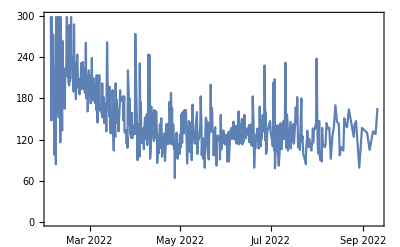

```mathematica
dlp=DateListPlot[ts]
```

### Interpolation

測定間隔がまばらなので間の値も推測できるよう補間関数を作成。

```mathematica
nts=Normal[ts];
```

```mathematica
nPts=Length[nts]
```

534

```mathematica
startDate=nts[[1,1]]
```

Wed 2 Feb 2022 16:45:00GMT+9

```mathematica
startTime=AbsoluteTime[nts[[1,1]]]
```

3852809100

```mathematica
endDate=nts[[-1,1]]
```

Sat 10 Sep 2022 18:03:00GMT+9

```mathematica
endTime=AbsoluteTime[nts[[-1,1]]]
```

3871821780

```mathematica
period=(endTime-startTime)/nPts//N
```

35604.3

```mathematica
endDate-startDate
```

220.054 days

```mathematica
nPts/(endDate-startDate)
```

2.42668 per day

```mathematica
ifn=Interpolation[ts]
```

InterpolatingFunction[…]

### Fourier

period 1

実際の測定回数から平均の測定間隔を算出し用いる。うまくいっているか確認。おおむね良いだろうと判断。

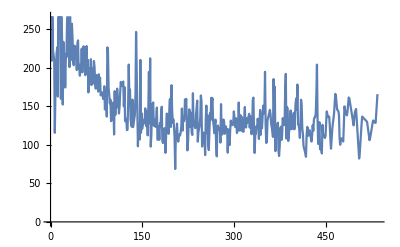
Interporation | -Graphics-
Original | -Graphics-

```mathematica
Grid[{{"Interporation",ListLinePlot[Table[ifn[t],{t,startTime,endTime,period}]]},{"Original",dlp}}]
```

等間隔データに対してフーリエを適応する。低周波側に大きなピークが見られる。このような場合、強い周期性がないことを示唆している。

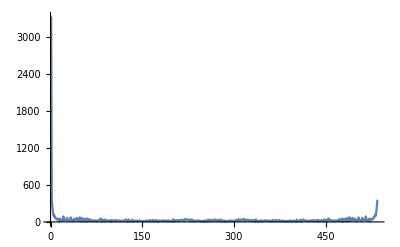

```mathematica
ListLinePlot[(fou=Fourier[Table[ifn[t],{t,startTime,endTime,period}]])//Abs,PlotRange->Full]
```

低周波側を除き、ある程度の強度がある周波数を確認する。20回弱、80回後の部分にピークが見られる。

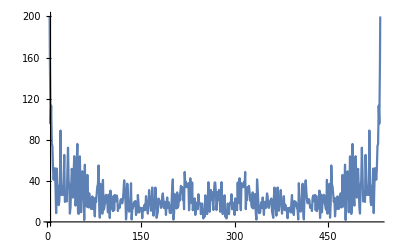

```mathematica
ListLinePlot[Fourier[Table[ifn[t],{t,startTime,endTime,period}]]//Abs,PlotRange->{{5,nPts-5},{0,200}}]
```

```mathematica
af=Abs[Fourier[Table[ifn[t],{t,startTime,endTime,period}]]];
```

```mathematica
largest=TakeLargest[af[[5;;nPts-5]],9]
```

{113.146,95.6597,88.9145,88.9145,76.0392,75.881,75.881,73.7351,73.7351}

```mathematica
max1=Sort[largest,"Largest"][[1]]
```

113.146

```mathematica
Position[af,max1]
```

{{6}}

```mathematica
nc=(Position[af,max1][[1,1]]-1)
```

5

218回の繰り返し、0.4日の周期。

```mathematica
(endTime-startTime)/60/60/24/nc//N
```

44.0108

もう一つ。

```mathematica
max3=Sort[largest,"Largest"][[3]]
```

88.9145

```mathematica
Position[af,max3]
```

{{21},{516}}

```mathematica
nc2=(Position[af,max3][[1,1]]-1)
```

20

5回の繰り返し、18日周期。

```mathematica
(endTime-startTime)/60/60/24/(nc2)//N
```

11.0027

period 2

1日4回の測定データを擬似的に作成。（おおよそ6、12、18時に測定しているので、24時の測定値を仮想的に作る）

```mathematica
period2=(endTime-startTime)/(endDate-startDate)[[1]]/4 (*1日4回*)
```

21600.

```mathematica
nPts2=Ceiling[(endTime-startTime)/period2]
```

881

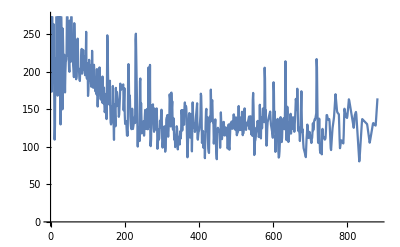
Interpolation | -Graphics-
Original | -Graphics-

```mathematica
Grid[{{"Interpolation",ListLinePlot[Table[ifn[t],{t,startTime,endTime,period2}]]},{"Original",dlp}}]
```

```mathematica
fou2=Fourier[Table[ifn[t],{t,startTime,endTime,period2}]];
```

```mathematica
largest2=TakeLargest[Abs[fou2[[5;;(nPts2-5)]]],10]
```

{148.327,124.592,115.714,115.714,104.109,104.109,93.3596,93.3596,88.2495,88.2495}

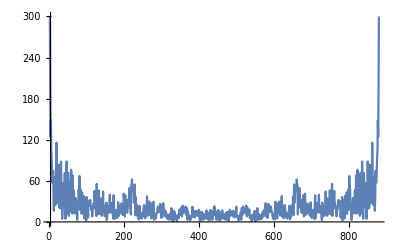

```mathematica
ListLinePlot[Fourier[Table[ifn[t],{t,startTime,endTime,period2}]]//Abs,PlotRange->{{5,nPts2-5},{0,300}}]
```

```mathematica
max11=Sort[largest2,"Largest"][[1]]
```

148.327

```mathematica
Position[Abs[fou2],max11]
```

{{6},{877}}

```mathematica
nc11=Position[Abs[fou2],max11][[1]]
```

{6}

```mathematica
(endTime-startTime)/60/60/24/(nc11)//N
```

{36.6757}

### ローパス

period 1

まず、逆フーリエで再現できるか確認。

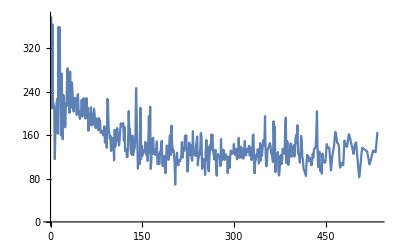
InverseFourier | -Graphics-
Original | -Graphics-

```mathematica
Grid[{{"InverseFourier",ListLinePlot[InverseFourier[fou],PlotRange->Full]},{"Original",dlp}}]
```

少しづつ、ローパスをかけていく。

```mathematica
fouLen=Length[fou]
```

535

```mathematica
np=150
```

150

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

535

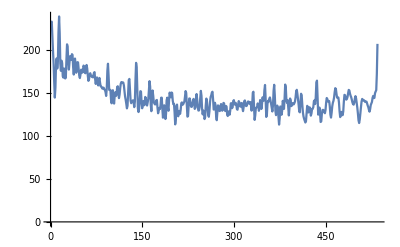

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
np=100
```

100

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

535

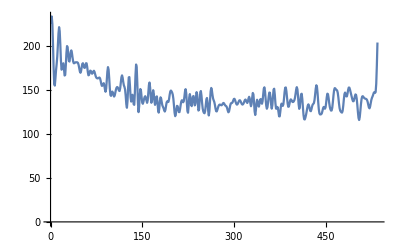

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
np=50
```

50

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
fullLen=((flt["total"]=Flatten[{flt[1],flt[2]}])//Length)
```

535

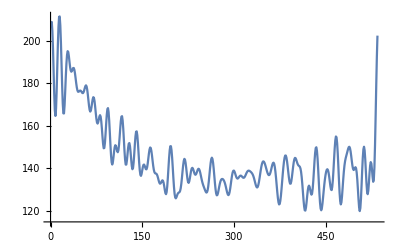

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
np=20
```

20

```mathematica
flt[1]=Table[1,{np}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
flt[2]=Table[0,{fouLen-np}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(flt["total"]=Flatten[{flt[1],flt[2]}])//Length
```

535

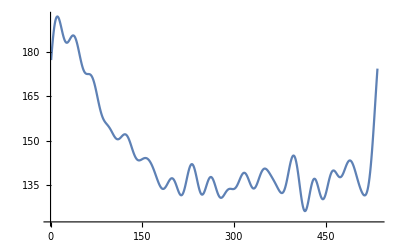

```mathematica
ListLinePlot[InverseFourier[fou*flt["total"]]//Abs]
```

```mathematica
InverseFourier[fou*flt["total"]]//Length
```

535

### EQ

補間データに対してエコライザーを通す。

```mathematica
createEQmanipulate[num_,vnameFou_String,vnameStep_String]:=Module[{tblstr,sliderstr},
tblstr="Table[Interpolation["<>ToString[Table["x"<>ToString[n],{n,num}]]<>"]"<>"[t],"<>"{t,1,"<>ToString[num]<>"-"<>ToString[vnameStep]<>","<>ToString[vnameStep]<>"}]";
sliderstr=StringTake[ToString[Table[{"x"<>ToString[n],0,1},{n,num}]],{2,-2}];
"Manipulate[{ListPlot["<>tblstr<>"],"<>"ListLinePlot[Abs[InverseFourier["<>vnameFou<>"*"<>tblstr<>"]]]},"<>sliderstr<>"]"
]
```

period 1

17帯域とする。

```mathematica
frac=17
```

17

```mathematica
step2=(frac-1)/fullLen//N
```

0.0299065

```mathematica
fullLen
```

535

フィルターのポイント数を合わせる。

```mathematica
Table[1,{t,1,frac-step2,step2}]//Length
```

535

```mathematica
createEQmanipulate[frac,"fou","step2"]//ToExpression
```